## Функции извлечения конкретнных данных из символьного XML представления поста

После того, как мы подгрузили все посты с Хабрахабра в формате символьных XML объектов, нам потребуется извлечь из них интересющую нас информацию. Для этого мы создадим ряд функций, представленных ниже.

Заголовок поста

```mathematica
extractData["Title"][data_]:=FirstCase[data,XMLElement["h1",{"class"->"post__title"},{spans_}]:>
Cases[{spans},XMLElement["span",{},{title_}]:>title,Infinity],Missing["NotAvailable"],Infinity]
```

Список хабов, в которых опубликован пост

```mathematica
extractData["Habs"][data_]:=Normal[FirstCase[data,XMLElement["div",{"class"->"hubs"},{hubs__}]:>Cases[{hubs},XMLElement["a",{___},{name_}]:>name,Infinity],Missing["NotAvailable"],Infinity]]
```

Дата и время публикации поста в формате абсолютного времени (для удобства дальнейшей работы).

```mathematica
dateConvert[date_,todayInput_]:=Module[{today,yesterday,step1,step2},today=DateList[todayInput][[{3,2,1}]];yesterday=DateList[DatePlus[todayInput,{-1,"Day"}]][[{3,2,1}]];step1=StringSplit[StringReplace[date,{"сегодня"->"today","вчера"->"yesterday"," в "->" ","января"->"1","февраля"->"2","марта"->"3","апреля"->"4","мая"->"5","июня"->"6","июля"->"7","августа"->"8","сентября"->"9","октября"->"10","ноября"->"11","декабря"->"12"}]," "];step2=Flatten[step1/.{"today"->today,"yesterday"->yesterday}]/.{x__,time_String}:>Flatten[{x,ToExpression/@StringSplit[time,":"]}];AbsoluteTime@If[Length[step2]==4,{today[[3]]}~Join~(ToExpression/@step2[[{2,1,3,4}]]),ToExpression/@step2[[{3,2,1,4,5}]]]]

extractData["DateAndTime"][data_,today_]:=With[{value=dateConvert[Cases[data,XMLElement["span",{"class"->"post__time_published"},{v_}]:>StringTrim[v],Infinity],today]},If[Head[value]===Missing,Missing["NotAvailable"],<|"PublicationAbsoluteTime"->value|>~Join~AssociationThread[{"PublicationHour","PublicationDayOfWeek","PublicationMonth","PublicationYear"},DateValue[value,{"Hour24","DayName","Month","Year"}]]]]
```

Рейтинг поста

```mathematica
extractData["Raiting"][data_]:=ToExpression[FirstCase[Cases[data,XMLElement["div",{"class"->"voting-wjt__counter voting-wjt__counter_positive js-mark"},{cases_}]:>cases,Infinity],XMLElement["span",___,{value_}]:>value,2,Infinity]]
```

Количество просмотров поста

```mathematica
extractData["PageViews"][data_]:=
With[{mystring=FirstCase[Cases[data,XMLElement["div",{"class"->"views-count_post",___},{cases_}]:>cases,Infinity],XMLElement["span",{"class"->"tab-item__value stats"},{values_}]:>values,2,Infinity]},
With[{nstring=If[StringContainsQ[mystring,","],StringReplace[mystring,","->""],If[StringContainsQ[mystring,"k"],StringReplace[mystring,"k"->"000"],mystring]]},
If[StringContainsQ[nstring,"k"],ToExpression[StringReplace[nstring,","->""]],ToExpression[nstring]
]
]
]
```

Статистика гиперссылок, приведенных в посте

```mathematica
extractData["HyperlinksStatistics"][data_]:=Reverse[Sort[Counts[Cases[FirstCase[data,XMLElement["div",{___,"class"->"content html_format",___},{content__}]:>{content},Missing["NotAvailiable"],Infinity],XMLElement["a",{___,"href"->link_},___]:>Quiet@Check[URLParse[link]["Domain"],Unevaluated[Sequence[]]],Infinity]]]]
```

Количество изображений, использованных в посте

```mathematica
extractData["ImageCount"][data_]:=Count[FirstCase[data,XMLElement["div",{___,"class"->"content html_format",___},{content__}]:>{content},Missing["NotAvailiable"],Infinity],XMLElement["img",__],Infinity]
```

Количество комментариев к посту

```mathematica
extractData["CommentCount"][data_]:=FirstCase[data,XMLElement["span",{"id"->"comments_count"},{n_}]:>ToExpression[n],Missing["NotAvailiable"],Infinity]
```

Количество видео, вставленных в пост

```mathematica
extractData["VideoCount"][data_]:=Count[FirstCase[data,XMLElement["div",{___,"class"->"content html_format",___},{content__}]:>{content},Missing["NotAvailiable"],Infinity],XMLElement["iframe",___],Infinity]
```

Текст поста в стандартизованной форме (устранены абзацы, все буквы сделаны прописными)

```mathematica
russianLowerCase=Thread[CharacterRange["А","Я"]->CharacterRange["а","я"]]~Join~{"Ё"->"ё"};

toRussianLowerCase[str_String]:=StringReplace[str,russianLowerCase];

extractData["PostText"][data_]:=ToLowerCase[toRussianLowerCase[StringReplace[StringReplace[StringJoin[FirstCase[data,XMLElement["div",{___,"class"->"content html_format",___},{content__}]:>{content},Missing["NotAvailiable"],Infinity]//.XMLElement[_,_,{string___}]:>string],"\n"|"\t"->" "]," "..->" "]]]
```

Статистика кодов, приведенных в посте

```mathematica
extractData["CodeStatistics"][data_]:=Reverse[Sort[Counts[Cases[FirstCase[data,XMLElement["div",{___,"class"->"content html_format",___},{content__}]:>{content},Missing["NotAvailiable"],Infinity],XMLElement["code",{___},{___}],Infinity]/.{XMLElement["code",{"class"->value_},{___}]:>value,XMLElement["code",{},_]->"SomeCode"}]]]
```

Ключевые слова

```mathematica
extractData["KeyWords"][data_]:=Cases[FirstCase[data,XMLElement["ul",{___,"class"->"tags icon_tag",___},{content___}]:>{content},Missing["NotAvailiable"],Infinity],XMLElement["a",{___},{keyWord_}]:>keyWord,Infinity]
```

## Создание базы данных постов Хабрахабра с помощью Dataset

Теперь подгрузим пути до всех файлов .mx, в которых хранятся посты:

```mathematica
Style[Short[linksToPosts=FileNames[{"*.mx"},FileNameJoin[{NotebookDirectory[],"HabInformation","Posts"}],20],14]]
```

```mathematica
Length[linksToPosts]
```

213679

Создадим функцию, которая будет создавать строку базы данных о постах Хабрахабра, которую мы получим ниже. Мы сделаем это с помощью созданных ранее функций, а также функции Association.

```mathematica
NowTime=Now
```

Sun 5 Feb 2017 16:15:54GMT+5.

```mathematica
postData[linkToFile_]:=With[
{data=Quiet[Import[linkToFile,"Expression",CharacterEncoding->"WindowsCyrillic"]],
downloadTime= NowTime},
<|"Title"->extractData["Title"][data],
"Habs"->extractData["Habs"][data],
"KeyWords"->extractData["KeyWords"][data],
"PostText"->extractData["PostText"][data],
"Raiting"->extractData["Raiting"][data],
"PageViews"->extractData["PageViews"][data],
"HyperlinksStatistics"->extractData["HyperlinksStatistics"][data],
"CodeStatistics"->extractData["CodeStatistics"][data],
"CommentCount"->extractData["CommentCount"][data],
"VideoCount"->extractData["VideoCount"][data_],
"ImageCount"->extractData["ImageCount"][data]|>~Join~(extractData["DateAndTime"][data,downloadTime])]
```

Наконец, сформируем с помощью функции Dataset базу данных постов Хабрахабра:

```mathematica
If[FileExistsQ[#],Get[#],
habrDataset=Dataset[ParallelTable[Check[postData[linksToPost],Print@linksToPost],{linksToPost,linksToPosts}]];
DumpSave[#,habrDataset]]&@FileNameJoin[{NotebookDirectory[],"HabInformation","habrDataset"<>".mx"}];
```

```mathematica
habrDataset=Select[habrDataset,UnsameQ[#,Null] &]
```

```mathematica
habrDataset = habrDataset[DeleteDuplicatesBy["PostText"]]
```

Dataset[<>]

```mathematica
DeleteMissing[habrDataset]
```

Dataset[<>]

```mathematica
Length[habrDataset]
```

170903

## Результаты обработки данных

Краткий анализ хабов

Найдем распределение количества хабов, в которых размещена статья:

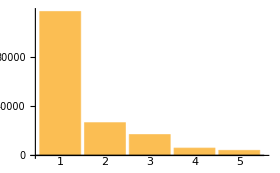
Dataset[<>]   -Graphics-

```mathematica
Row[{#,"   ",BarChart[#,ImageSize->280,ChartLabels->Automatic]}]&@Reverse[Sort[habrDataset[Counts,"Habs",Length]]]
```

Представим этот фрагмент Dataset в виде таблицы:

```mathematica
Grid[{{Style["Количество хабов,\nв которых размещена статья",TextAlignment->Center],"Количество статей","Процент статей"}}~Join~Transpose[{Normal[Keys[#]],Sequence@@(Function[{#,N@Round[100#/Total[#],1/10]}]@Normal[Values[#]])}&@Reverse[Sort[habrDataset[Counts,"Habs",Length]]]],ItemStyle->{FontFamily->"Myriad Pro Cond",22},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]]
```

Количество хабов,
в которых размещена статья | Количество статей | Процент статей
1 | 117226 | 68.6
2 | 26664 | 15.6
3 | 16983 | 9.9
4 | 5956 | 3.5
5 | 4074 | 2.4

Найдем самые большие Хабы по количеству статей:

```mathematica
Reverse[Sort[Counts[Flatten[habrDataset[All,"Habs"]]]]]
```

Dataset[<>]

Если рассмотреть только уникальные статьи (относящиеся только к одному хабу, то картина несколько изменится):

```mathematica
Reverse[Sort[Counts[Flatten@Select[habrDataset[All,"Habs"],Length[#]==1&]]]]
```

Dataset[<>]

Также, найдем количество постов компаний (здесь не учитываются посты, написанные компанией только для своего блога):

```mathematica
Reverse[Sort[Counts[Cases[Flatten[habrDataset[All,"Habs"]],x_/;StringMatchQ[x,"Блог"~~___]]]]]
```

Dataset[<>]

Количество статей в зависимости от времени

Создадим функцию, визуализации количества опубликованных статей как на всем Хабрахабре, так и в некотором хабе:

```mathematica
habPostCount[habName_:_]:=Module[{postByMonth,postsByYear,gridLines},

{postByMonth,postsByYear}=Table[Counts@habrDataset[Select[MemberQ[#Habs,habName]&],"PublicationAbsoluteTime"][All,DateList[#][[timeSpec]]&],{timeSpec,{{1,2},{1}}}];

gridLines=Table[{DatePlus[{2005,1,1},{3n,"Month"}],If[Mod[n,4]==0,Directive[{Thick,Gray}],LightGray]},{n,1,50}];
Grid[Transpose@{DateListPlot[#[[1]],PlotStyle->Orange,Filling->Axis,PlotRange->All,GridLines->{gridLines,None},ImageSize->700,InterpolationOrder->1,PlotLabel->Style[#[[2]],22,FontFamily->"Myriad Pro Cond"],ImagePadding->{{40,5},{20,5}}]&/@{{postByMonth,If[habName===_,"Количество постов, публикуемых на Хабрахабре за месяц","Количество постов, публикуемых в хабе "<>habName<>" за месяц"]},{postsByYear,If[habName===_,"Количество постов, публикуемых на Хабрахабре за год","Количество постов, публикуемых в хабе "<>habName<>" за год"]}}}]]
```

Посмотрим на результаты ее работы. Из полученных графиков видно, что в настоящий момент, по-видимому, наблюдается выход количества публикуемых в год на Хабрахабре постов на плато, приближаясь к значению 11000 постов в год.

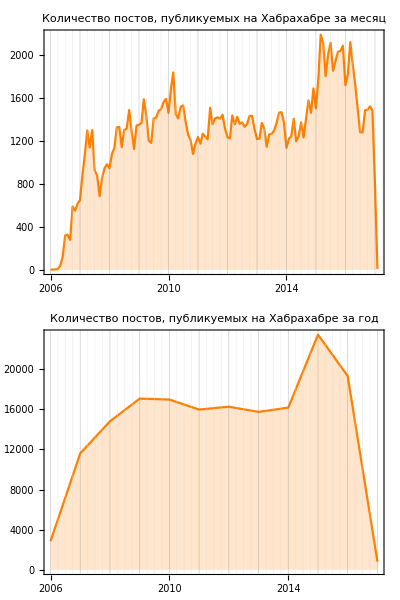

```mathematica
habPostCount[]
```

Начиная с 2012 года наблюдается стремительный рост публикаций в хабе “Математика”:

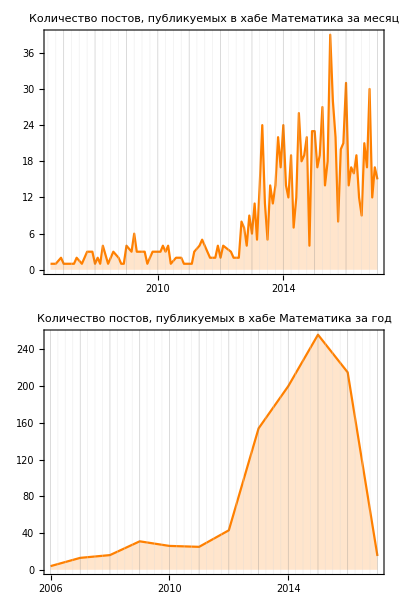

```mathematica
habPostCount["Математика"]
```

С 2011 года можно наблюдать затухание интереса к Flash:

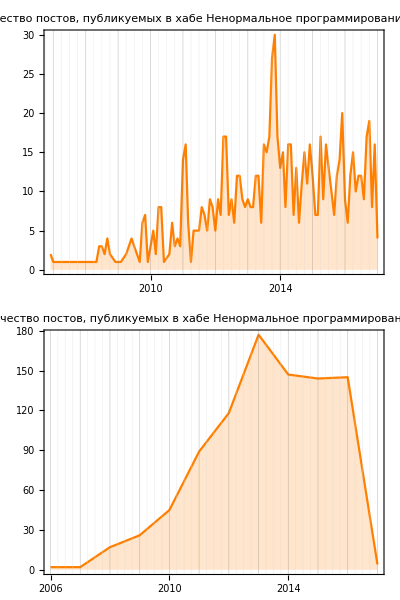

```mathematica
habPostCount["Ненормальное программирование"]
```

В то же время, с 2010 года хаб “Game Development” растет просто как на дрожжах:

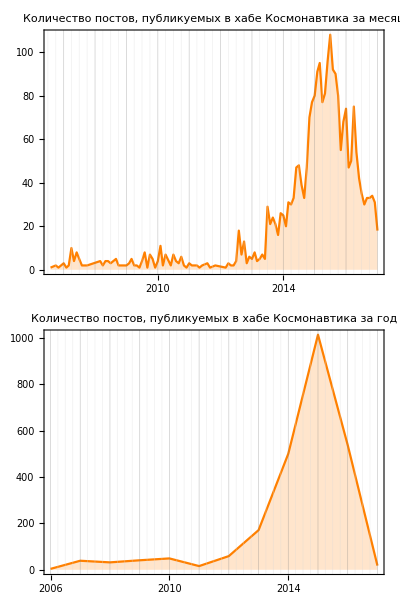

```mathematica
habPostCount["Космонавтика"]
```

Что интересно, в хаб “Хабрахабр” поступает все меньше статей.

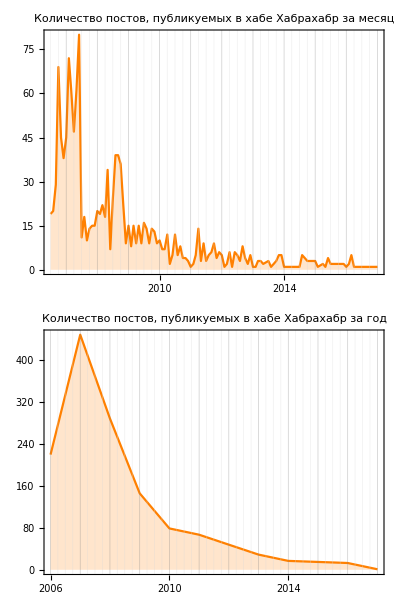

```mathematica
habPostCount["Хабрахабр"]
```

Количество изображений (видео), используемых в постах в зависимости от времени

Создадим функцию, визуализации количества изображений (или видео), в опубликованных постах, как на всем Хабрахабре, так и в некотором хабе:

```mathematica
habImageOrVideoCount[type_,habName_:_,function_:Total]:=Module[{postByMonth,postsByYear,gridLines,typeName,functionName,endOfString},

{postByMonth,postsByYear}=Table[habrDataset[Select[MemberQ[#Habs,habName]&],{"PublicationAbsoluteTime"->(DateList[#][[timeSpec]]&),type->Identity}][GroupBy[Key["PublicationAbsoluteTime"]],function,type],{timeSpec,{{1,2},{1}}}];

gridLines=Table[{DatePlus[{2005,1,1},{3n,"Month"}],If[Mod[n,4]==0,Directive[{Thick,Gray}],LightGray]},{n,1,50}];
typeName=If[type==="ImageCount","изображений","видео"];
functionName=If[function===Total,"Количество ","Среднее число "];
endOfString=If[function===Total,"за месяц","в течении месяца"];
Grid[Transpose@{DateListPlot[#[[1]],PlotStyle->Orange,Filling->Axis,PlotRange->All,GridLines->{gridLines,None},ImageSize->700,InterpolationOrder->1,PlotLabel->Style[#[[2]],22,FontFamily->"Myriad Pro Cond"],ImagePadding->{{50,5},{30,5}}]&/@{{postByMonth,If[habName===_,functionName<>typeName<>", публикуемых на Хабрахабре "<>If[function===Total,"за месяц","в течении месяца (в одной статье)"],functionName<>typeName<>", публикуемых в хабе "<>habName<>If[function===Total," за месяц","в течении месяца (в одной статье)"]]},{postsByYear,If[habName===_,functionName<>typeName<>", публикуемых на Хабрахабре "<>If[function===Total,"за год","в течении года (в одной статье)"],functionName<>typeName<>", публикуемых в хабе "<>habName<>If[function===Total," за год","в течении года (в одной статье)"]]}}}]]
```

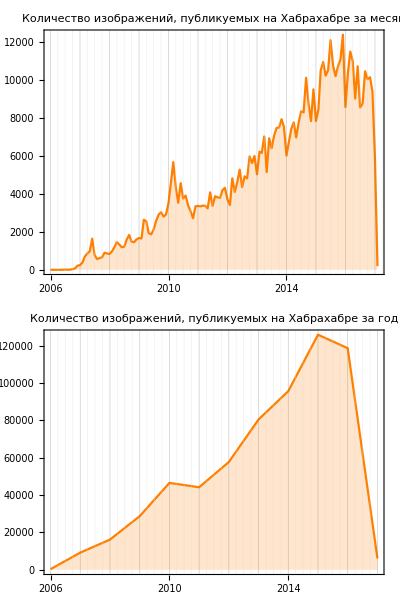

```mathematica
habImageOrVideoCount["ImageCount"]
```

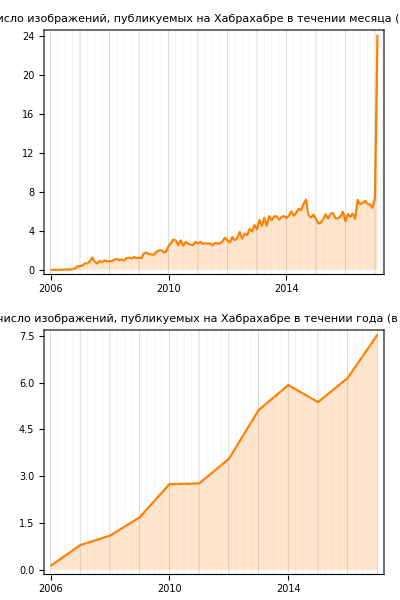

```mathematica
habImageOrVideoCount["ImageCount",_,Mean]
```

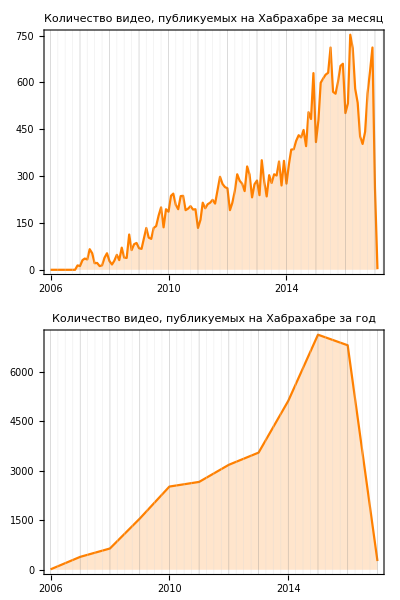

```mathematica
habImageOrVideoCount["VideoCount"]
```

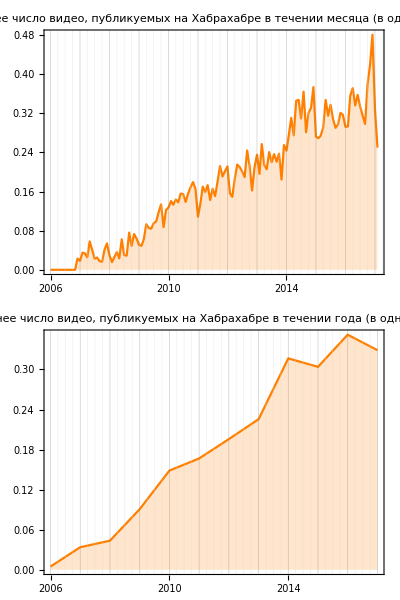

```mathematica
habImageOrVideoCount["VideoCount",_,Mean]
```

Посмотрим на некоторые хабы:

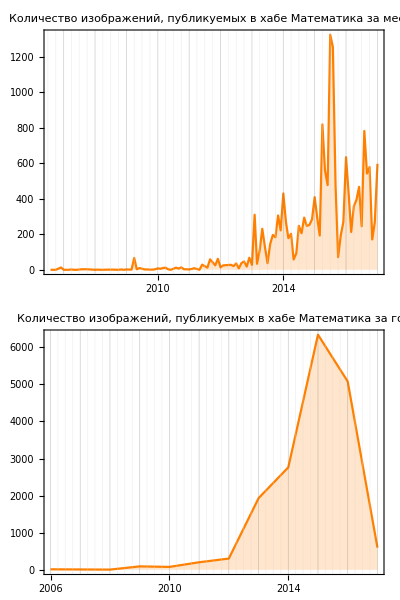

```mathematica
habImageOrVideoCount["ImageCount","Математика"]
```

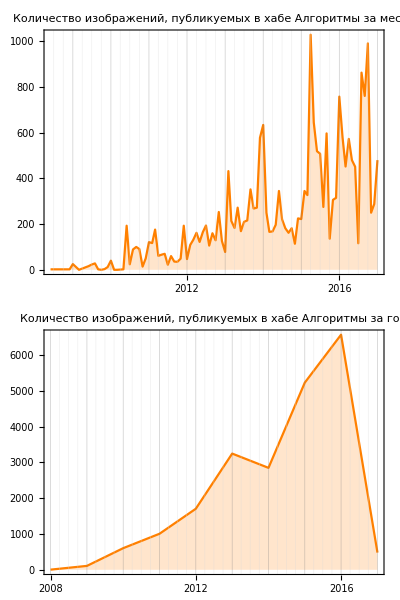

```mathematica
habImageOrVideoCount["ImageCount","Алгоритмы"]
```

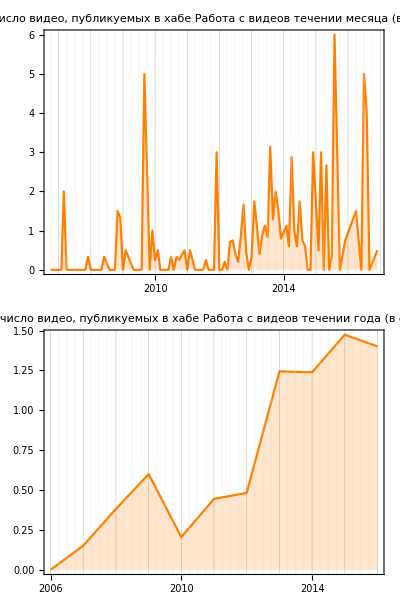

```mathematica
habImageOrVideoCount["VideoCount","Работа с видео",Mean]
```

Облака ключевых слов Хабрахабра и отдельных хабов

Найдем список количеств употребления ключевых слов среди всех анализируемых постов на Хабрахабре:

```mathematica
allHabrKeyWords=Reverse[Sort[Counts[Flatten[habrDataset[All,"KeyWords"]]]]]
```

Dataset[<>]

Выберем 150 наиболее распространенных среди них:

```mathematica
top150HabrKeyWords=Normal[allHabrKeyWords[[1;;150]]]
```

<|javascript→3166,android→3147,google→3034,php→2620,linux→2595,Google→2309,microsoft→2102,программирование→1954,стартапы→1927,apple→1858,java→1812,социальные сети→1787,python→1723,игры→1693,стартап→1680,разработка→1526,дизайн→1419,Microsoft→1400,безопасность→1333,Apple→1271,Android→1268,видео→1235,css→1196,.net→1189,open source→1188,реклама→1181,интернет→1152,информационная безопасность→1123,windows→1109,iphone→1106,конференция→1034,обзор→1004,юмор→1000,ios→978,статистика→972,яндекс→967,юзабилити→927,хабрахабр→927,html→882,маркетинг→863,facebook→860,тестирование→860,хостинг→851,html5→841,гаджеты→835,управление проектами→826,перевод→819,образование→804,конкурс→804,бизнес→802,новости→801,ubuntu→799,c++→792,firefox→782,космос→781,браузеры→771,работа→770,ruby→763,роботы→756,web-разработка→754,инвестиции→750,jquery→740,opera→728,поиск→724,Linux→704,обучение→685,музыка→685,twitter→648,iPhone→647,книги→643,iOS→637,mail.ru→633,оптимизация→632,arduino→622,mysql→619,будущее→614,мобильные приложения→611,Яндекс→610,сервисы→605,веб-разработка→588,копирайт→587,фриланс→587,алгоритмы→578,веб-дизайн→570,искусственный интеллект→555,дайджест→547,история→546,node.js→543,c#→539,flash→531,вконтакте→528,ссылки→524,технологии→523,умный дом→521,samsung→512,Веб 2.0→512,виртуализация→508,интервью→507,security→506,смартфоны→506,api→504,робототехника→497,Intel→487,интерфейсы→487,nokia→471,космонавтика→471,домены→466,PHP→462,идея→461,спам→460,nginx→452,финансы→452,электронная коммерция→449,монетизация→448,наука→448,ноутбук→446,аналитика→442,взлом→441,блогосфера→436,смартфон→428,Facebook→426,c→424,Windows→420,ruby on rails→420,gamedev→418,C++→418,google chrome→413,интернет-магазин→413,js→412,США→412,автоматизация→411,django→410,skype→408,game development→408,Nokia→406,cms→406,общение→403,JavaScript→400,cisco→399,производительность→399,авторское право→398,visual studio→397,интерфейс→397,youtube→396,C#→395,железо→395,windows phone→389,Samsung→387,web 2.0→386,математика→385|>

Создадим из них облако слов, в котором размер слова (или словосочетания) прямо пропорционален количеству его указаний:

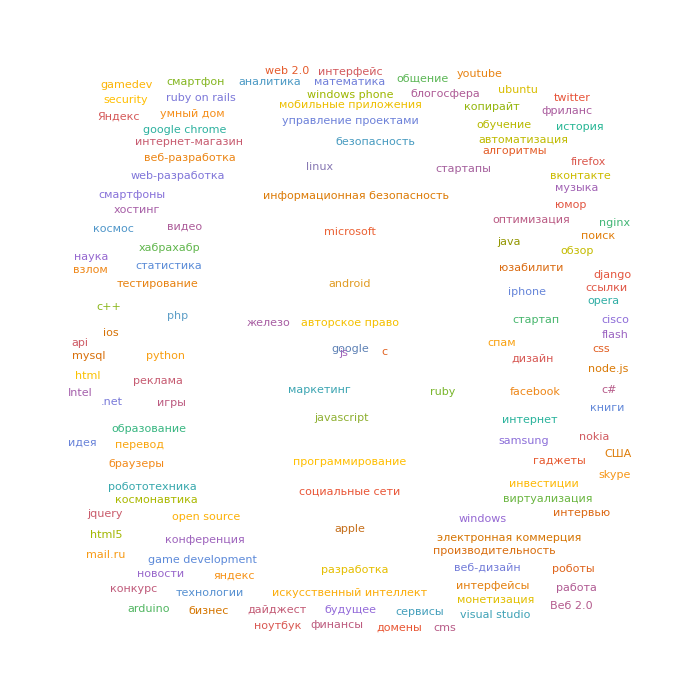

```mathematica
Quiet@WordCloud[top150HabrKeyWords,ImageSize->{700,700},FontFamily->"Myriad Pro Cond",MaxItems->All]
```

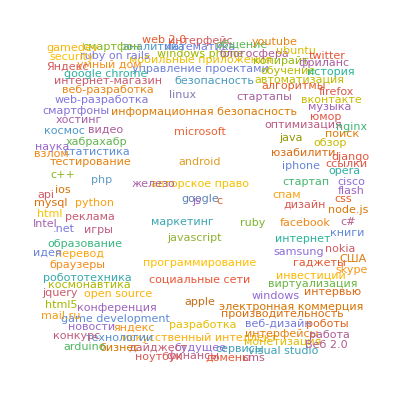

```mathematica
Show[%66,ImageSize->Full]
```

Мы также можем создать из некоторой строки маску:

```mathematica
mask=Binarize@ColorNegate@Rasterize@Style["HA\nBR",100,FontFamily->"Arial",Bold,LineSpacing->{0.7,0,0}]
```

-Graphics-

и сделать на ее основе облако слов, содержащее уже 750 самых распространненных ключевых слов (словосочетаний):

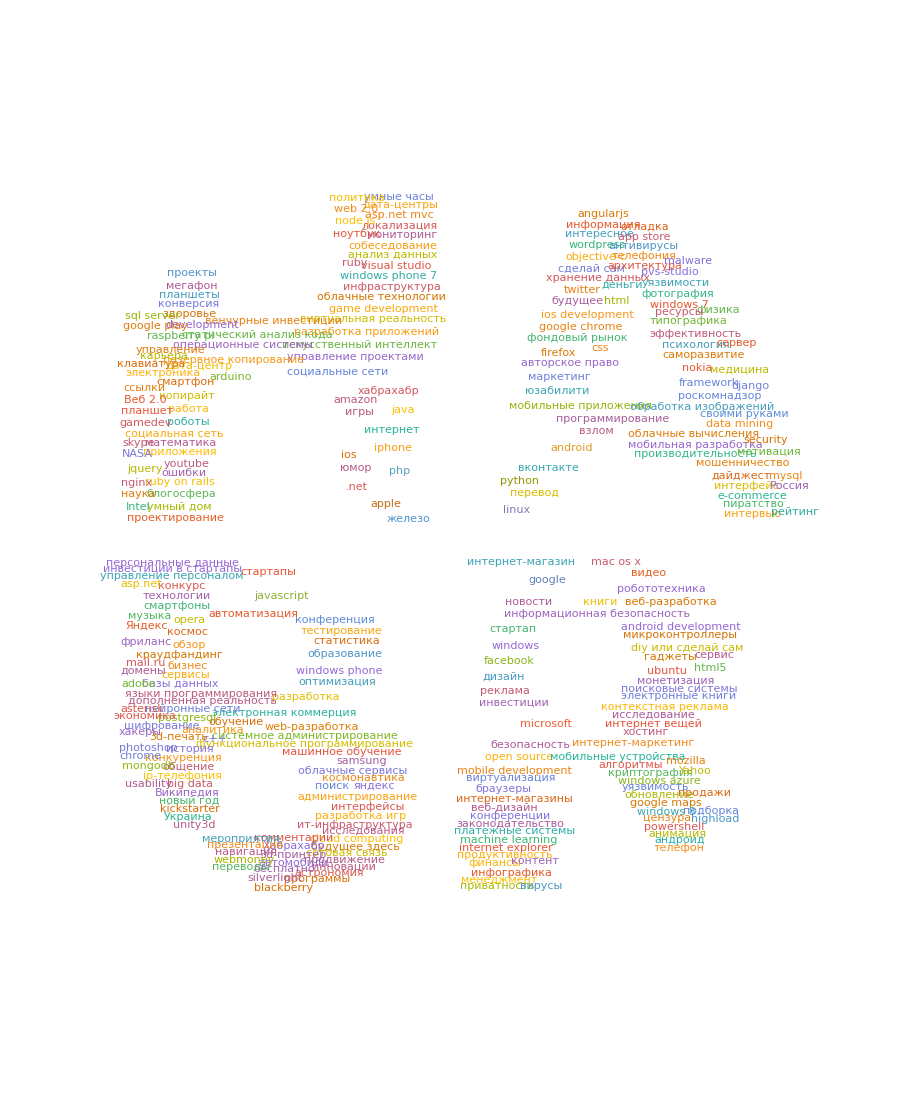

```mathematica
Quiet@WordCloud[Normal[allHabrKeyWords[[1;;500]]],mask,ImageSize->900,FontFamily->"Myriad Pro Cond",WordOrientation->"Random", MaxItems->All]
```

Можно также сделать облако слов в любой форме:

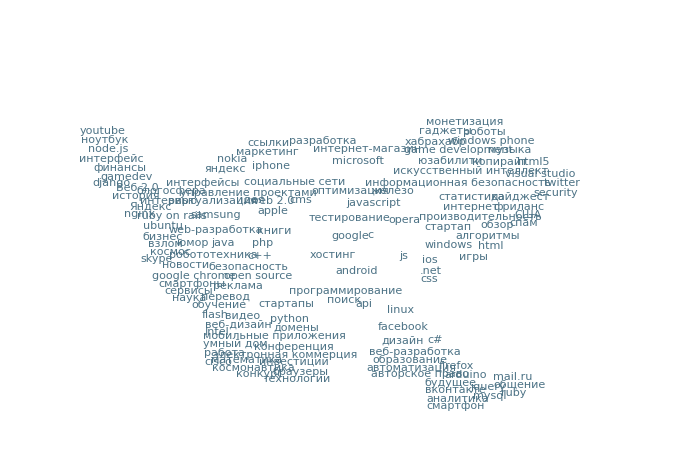

```mathematica
Quiet@WordCloud[Normal[allHabrKeyWords[[1;;150]]],Binarize@ColorNegate@Rasterize@#,ImageSize->700,FontFamily->"Myriad Pro Cond",ColorFunction->DominantColors[#][[2]],MaxItems->All]&@-Graphics-
```

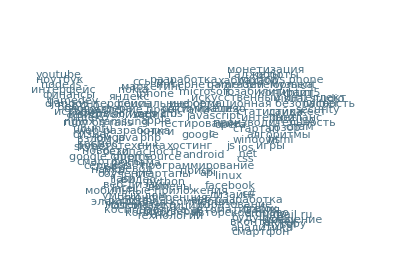

```mathematica
Show[%73,ImageSize->Full]
```

Теперь создадиф функцию, которая будет визуализировать облака самых популярных ключевых слов некоторого хаба (по умолчанию будет использоваться 100 слов):

```mathematica
habWordCloud[habName_,n_:100]:=Module[{keyWords=Normal[Reverse[Sort[Counts[Flatten[habrDataset[All,{"Habs","KeyWords"}][Select[MemberQ[#Habs,habName]&],"KeyWords"]]]]][[1;;n]]]},
WordCloud[keyWords, ImageSize->1000,FontFamily->"Myriad Pro Cond", MaxItems->All]]
```

100 ключевых слова хаба “Математика”:

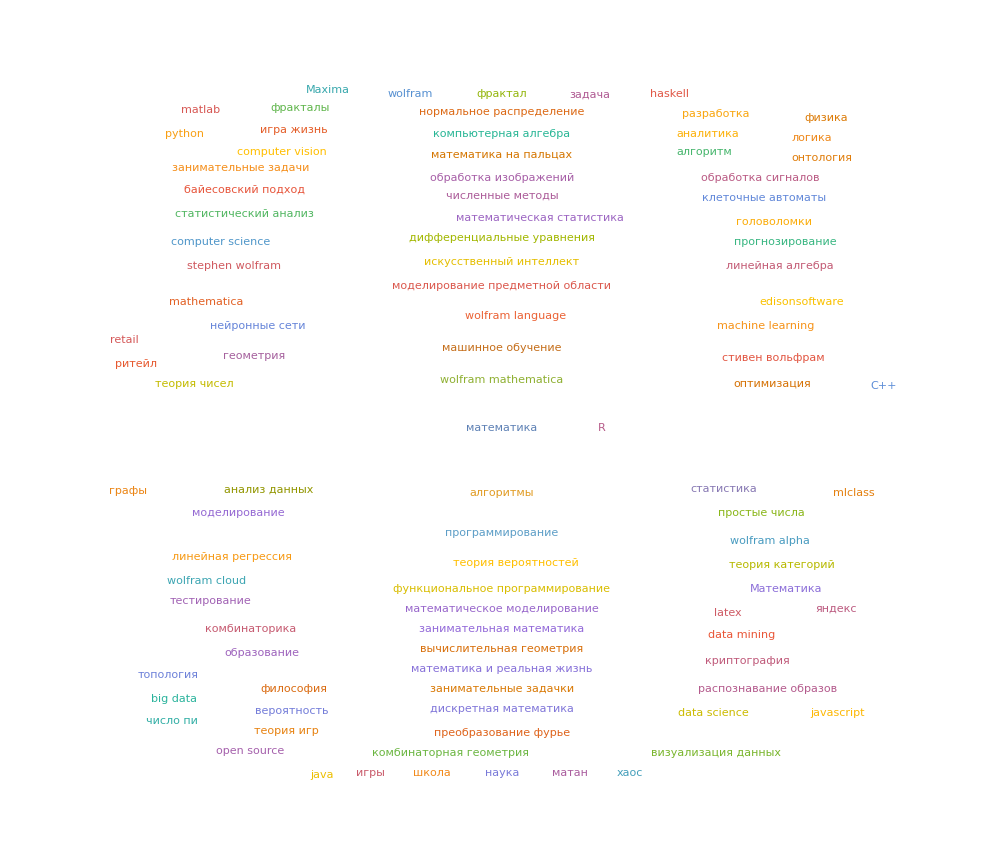

```mathematica
habWordCloud["Математика"]
```

30 ключевых слов хаба “Математика”:

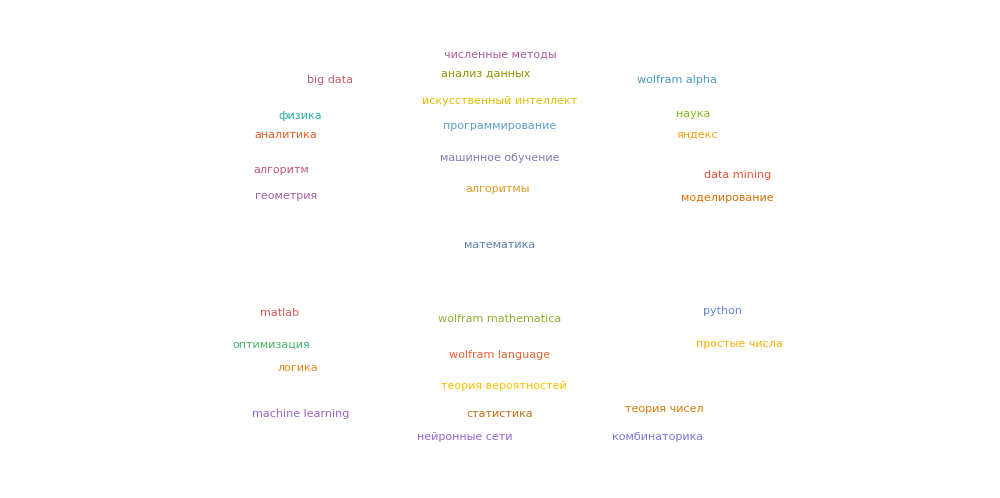

```mathematica
habWordCloud["Математика",30]
```

Ключевые слова хаба “Программирование”:

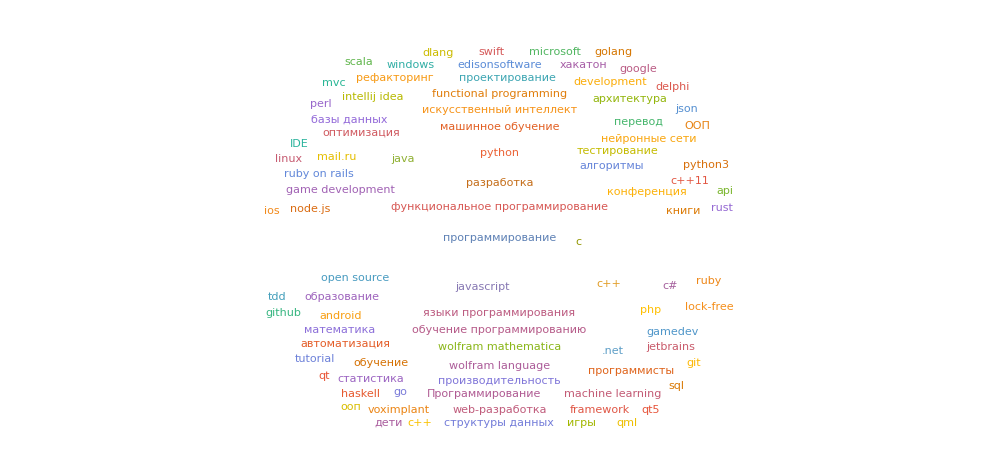

```mathematica
habWordCloud["Программирование"]
```

Ключевые слова хаба “JAVA”:

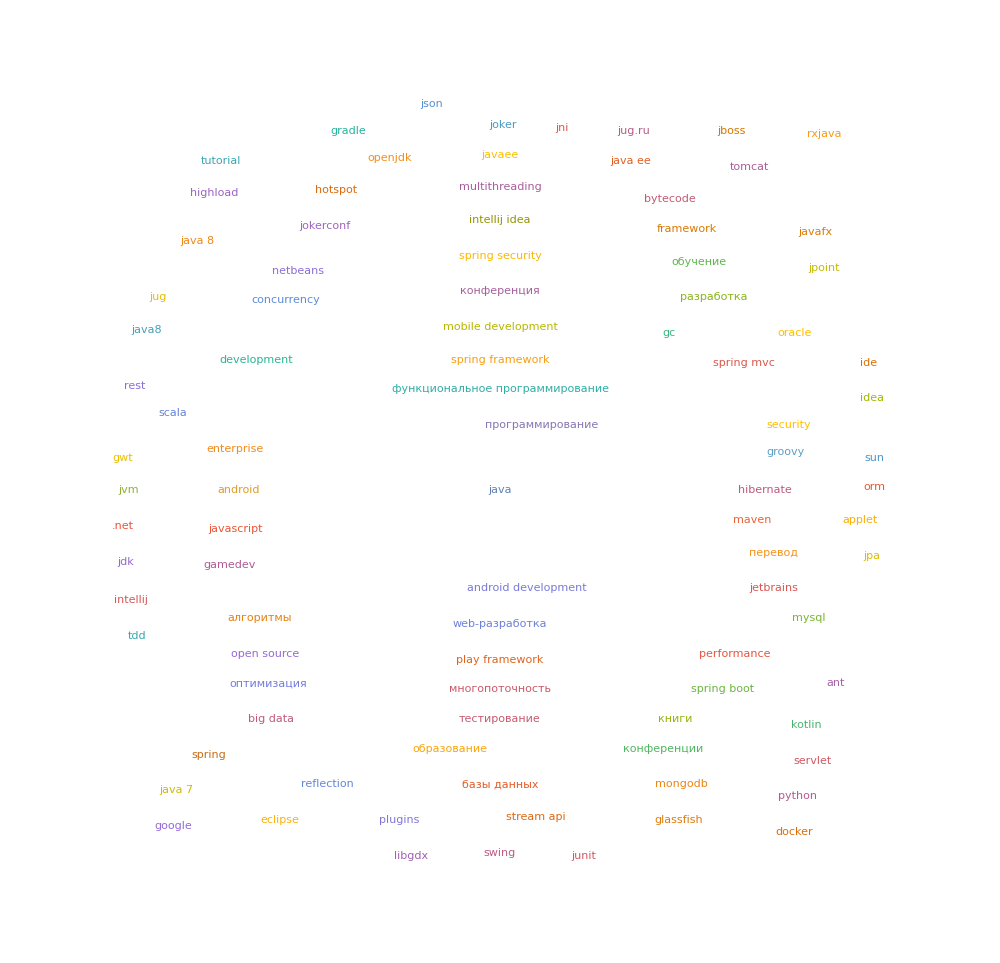

```mathematica
habWordCloud["Java"]
```

200 ключевых слов хаба “Open source”:

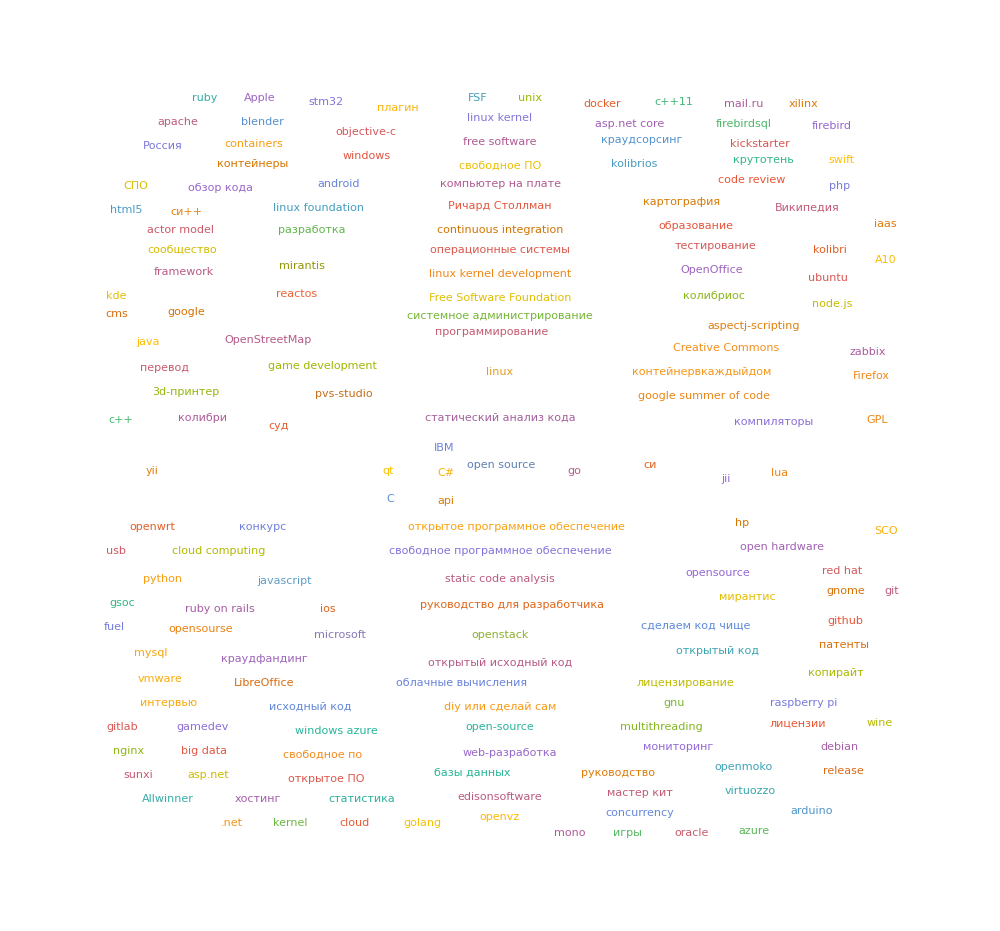

```mathematica
habWordCloud["Open source",200]
```

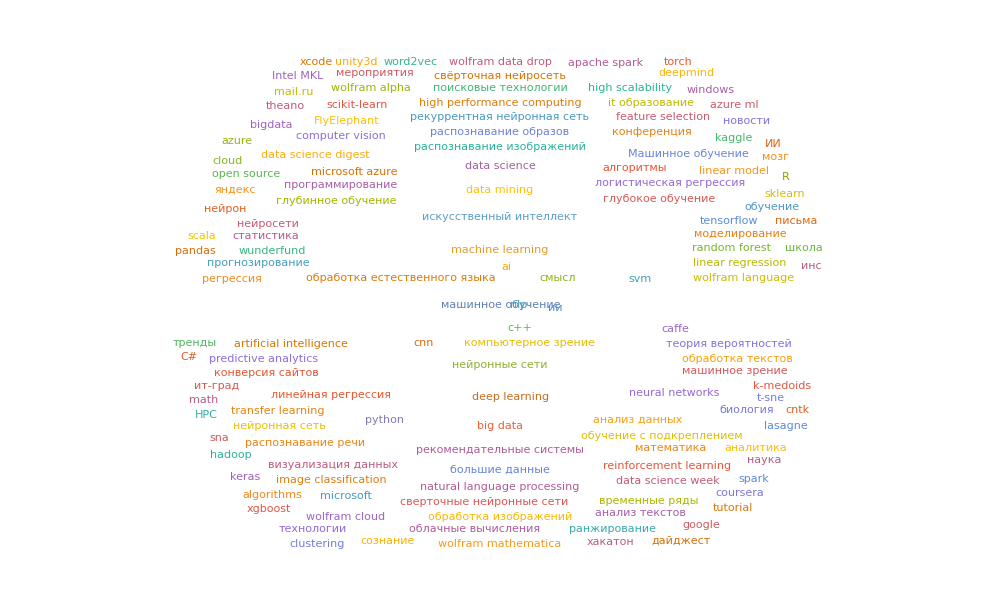

```mathematica
habWordCloud["Машинное обучение",150]
```

+Сайты, на которые ссылаются в статьях на Хабрахабре

Создадим функцию, которая будет показывать сайты, на которые чаще всего ссылаются как на Хабрахабре вообще, так и в некотором хабе:

```mathematica
habHyperlinksCount[habName_:_,deleteFirstLink_:False]:=Module[{hyperlinks=Reverse[Sort[Delete[Merge[Flatten[habrDataset[All,{"Habs","HyperlinksStatistics"}][Select[MemberQ[#Habs,habName]&],"HyperlinksStatistics"]],Total],Key[None]]]],length},
length=Length[hyperlinks];
With[{top20=hyperlinks[[If[deleteFirstLink,2,1];;If[length<20,length,20]]],top50=hyperlinks[[If[deleteFirstLink,2,1];;If[length<50,length,50]]]},Grid[{{Grid[{{"Сайт","Количество ссылок"}}~Join~Transpose[{Normal[Keys[top20]],Normal[Values[top20]]}],ItemStyle->{FontFamily->"Myriad Pro Cond",18},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]],Quiet@WordCloud[Normal@top50, ImageSize -> {600,500}, FontFamily -> "Myriad Pro Cond", MaxItems -> All,ColorFunction->"Rainbow"]}}]]]
```

Найдем сайты, на которые чаще всего ссылаются на Хабрахабре:

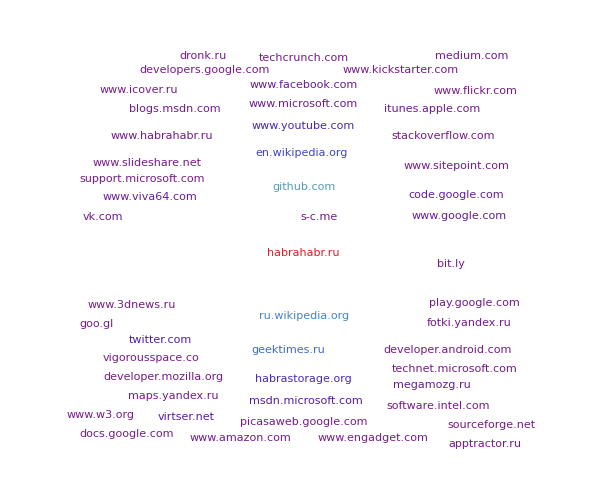
Сайт | Количество ссылок
habrahabr.ru | 109344
github.com | 38304
ru.wikipedia.org | 30150
geektimes.ru | 23976
en.wikipedia.org | 16918
habrastorage.org | 11505
www.youtube.com | 9862
twitter.com | 8138
msdn.microsoft.com | 6350
virtser.net | 5675
code.google.com | 4864
megamozg.ru | 4740
www.google.com | 4253
www.viva64.com | 3923
www.facebook.com | 3446
www.microsoft.com | 3296
vk.com | 3089
medium.com | 2756
itunes.apple.com | 2633
play.google.com | 2551 | -Graphics-

```mathematica
habHyperlinksCount[]
```

Картина становится яснее, если убрать главный источник ссылок — сам Хабрахабр.

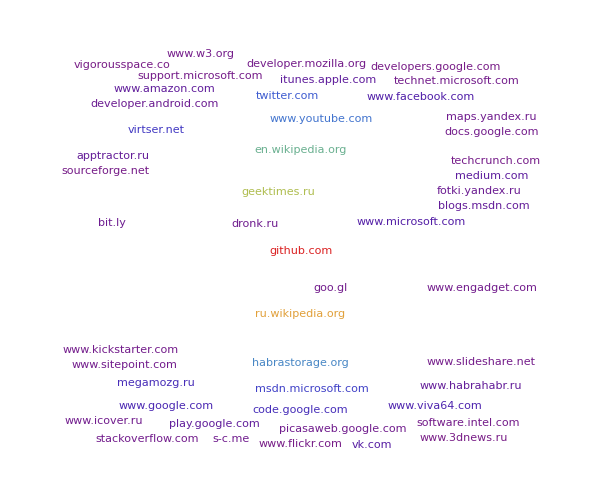
Сайт | Количество ссылок
github.com | 38304
ru.wikipedia.org | 30150
geektimes.ru | 23976
en.wikipedia.org | 16918
habrastorage.org | 11505
www.youtube.com | 9862
twitter.com | 8138
msdn.microsoft.com | 6350
virtser.net | 5675
code.google.com | 4864
megamozg.ru | 4740
www.google.com | 4253
www.viva64.com | 3923
www.facebook.com | 3446
www.microsoft.com | 3296
vk.com | 3089
medium.com | 2756
itunes.apple.com | 2633
play.google.com | 2551 | -Graphics-

```mathematica
habHyperlinksCount[_,True]
```

Найдем сайты, на которые чаще всего ссылаются в хабе “Математика” (при этом мы везде удалим сам Хабрахабр, так как на него всюду ссылаются, что очевидно, чаще всего):

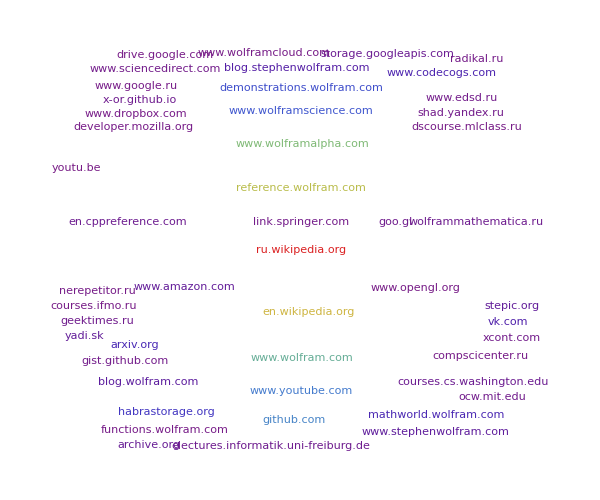
Сайт | Количество ссылок
ru.wikipedia.org | 829
en.wikipedia.org | 584
reference.wolfram.com | 534
www.wolframalpha.com | 410
www.wolfram.com | 345
github.com | 232
www.youtube.com | 213
www.wolframscience.com | 155
demonstrations.wolfram.com | 143
habrastorage.org | 107
arxiv.org | 83
mathworld.wolfram.com | 80
www.codecogs.com | 73
vk.com | 64
blog.stephenwolfram.com | 56
blog.wolfram.com | 46
www.stephenwolfram.com | 42
stepic.org | 39
yadi.sk | 38 | -Graphics-

```mathematica
habHyperlinksCount["Математика",True]
```

Теперь посмотрим, скажем, на хаб “Разработка под iOS”:

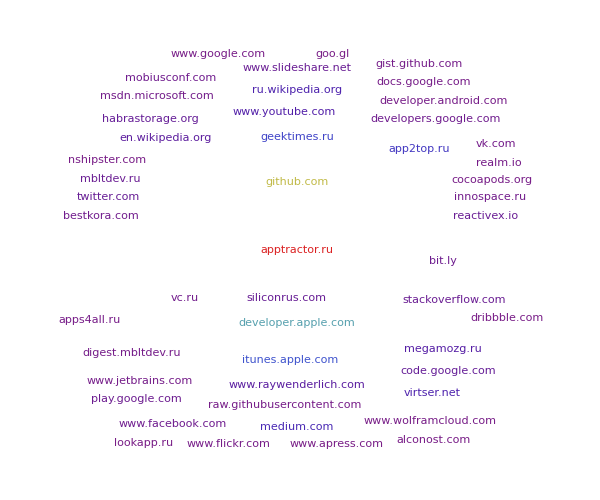
Сайт | Количество ссылок
apptractor.ru | 2087
github.com | 1386
developer.apple.com | 748
itunes.apple.com | 377
geektimes.ru | 317
app2top.ru | 269
medium.com | 207
virtser.net | 173
ru.wikipedia.org | 173
www.youtube.com | 148
megamozg.ru | 136
www.raywenderlich.com | 120
en.wikipedia.org | 113
code.google.com | 86
habrastorage.org | 85
siliconrus.com | 80
twitter.com | 78
www.slideshare.net | 74
reactivex.io | 74 | -Graphics-

```mathematica
habHyperlinksCount["Разработка под iOS",True]
```

А вот хаб “.NET”:

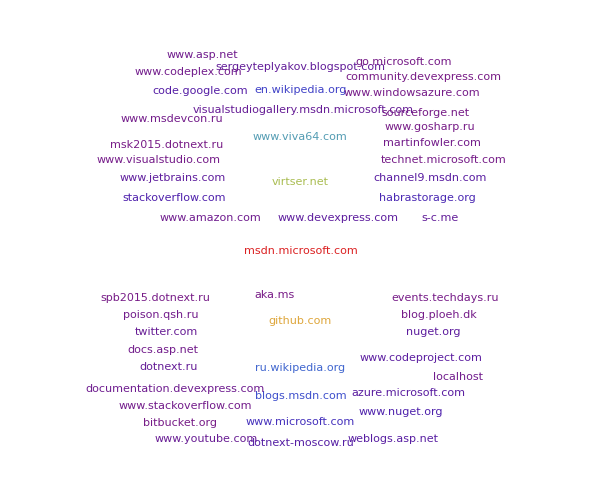
Сайт | Количество ссылок
msdn.microsoft.com | 1839
github.com | 1413
virtser.net | 1119
www.viva64.com | 645
ru.wikipedia.org | 411
blogs.msdn.com | 336
en.wikipedia.org | 290
www.microsoft.com | 229
habrastorage.org | 191
www.nuget.org | 162
stackoverflow.com | 160
code.google.com | 136
dotnext-moscow.ru | 134
weblogs.asp.net | 127
channel9.msdn.com | 124
azure.microsoft.com | 121
www.codeproject.com | 119
nuget.org | 114
www.devexpress.com | 113 | -Graphics-

```mathematica
habHyperlinksCount[".NET",True]
```

Коды, которые приводят в статьях на Хабрахабре

Найдем долю статей, в которых нет вставок кода (здесь возможна серьезная погрешность, так как не всегда код вставляется авторами с помощью специального тэга — скажем, в этом посте он вставлен в виде изображений).

```mathematica
N[100(Count[#,<||>]/Length[#])]&@habrDataset[All,"CodeStatistics"]
```

81.0191

Создадим функцию, которая будет показывать статистику языков вставок кода в посты, как на Хабрахабре вообще, так и в некотором хабе. При этом, если автор не указал код, то такой фрагмент будет помечен названием “SomeCode”. Также, здесь мы не производим обработку названий языков, указанных авторами.

```mathematica
habCodeCount[habName_:_,deleteFirstLink_:False]:=Module[{hyperlinks=Reverse[Sort[Delete[Merge[Flatten[habrDataset[All,{"Habs","CodeStatistics"}][Select[MemberQ[#Habs,habName]&],"CodeStatistics"]],Total],Key[None]]]],length},
length=Length[hyperlinks];
With[{top20=hyperlinks[[If[deleteFirstLink,2,1];;If[length<20,length,20]]],top50=hyperlinks[[If[deleteFirstLink,2,1];;If[length<50,length,50]]]},Grid[{{Grid[{{"Код","Количество фрагментов кода"}}~Join~Transpose[{Normal[Keys[top20]],Normal[Values[top20]]}],ItemStyle->{FontFamily->"Myriad Pro Cond",18},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]],Quiet@WordCloud[Normal@top50, ImageSize -> {600,500}, FontFamily -> "Myriad Pro Cond", MaxItems -> All,ColorFunction->"Rainbow"]}}]]]
```

Найдем распределение языков вставок кода для всего Хабрахабра:

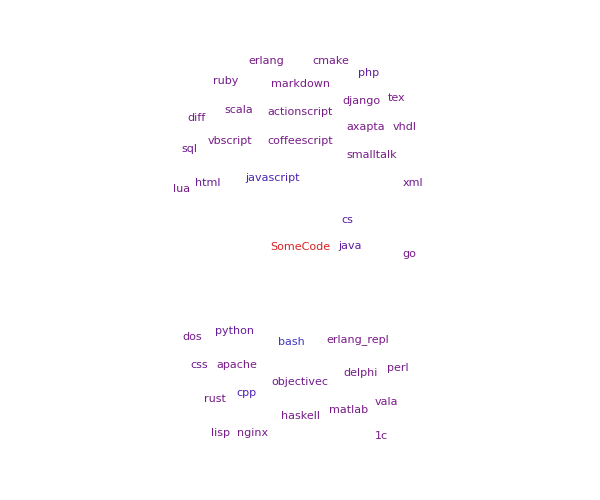
Код | Количество фрагментов кода
SomeCode | 303511
bash | 36402
javascript | 22867
cpp | 20197
java | 12091
cs | 11796
php | 10865
python | 9164
html | 6957
xml | 5115
sql | 5092
css | 4077
ruby | 3432
objectivec | 3198
haskell | 1429
dos | 1317
perl | 1301
scala | 1260
delphi | 1158
go | 1134 | -Graphics-

```mathematica
habCodeCount[]
```

Картина станет более ясной, если удалить вставки, у которых не указан язык программирования:

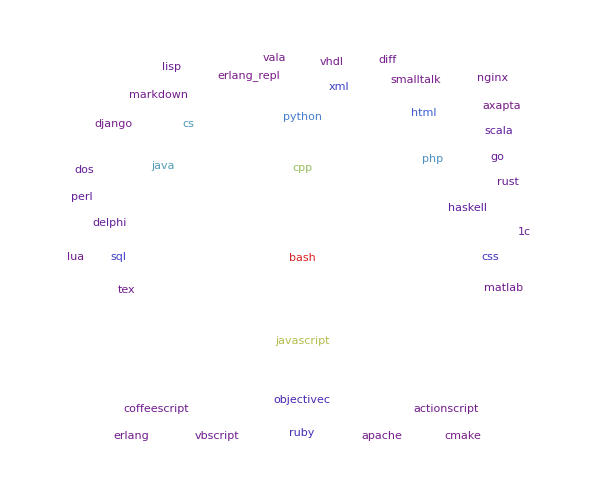
Код | Количество фрагментов кода
bash | 36402
javascript | 22867
cpp | 20197
java | 12091
cs | 11796
php | 10865
python | 9164
html | 6957
xml | 5115
sql | 5092
css | 4077
ruby | 3432
objectivec | 3198
haskell | 1429
dos | 1317
perl | 1301
scala | 1260
delphi | 1158
go | 1134 | -Graphics-

```mathematica
habCodeCount[_,True]
```

Картина становится яснее, если убрать главный источник ссылок — сам Хабрахабр.

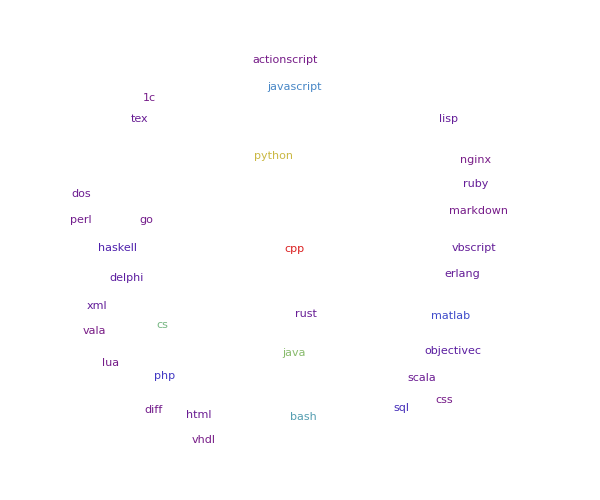
Код | Количество фрагментов кода
cpp | 1054
python | 722
java | 542
cs | 485
bash | 362
javascript | 293
matlab | 167
php | 130
sql | 105
haskell | 72
objectivec | 49
delphi | 47
xml | 36
vbscript | 35
lisp | 34
ruby | 33
erlang | 33
rust | 29
tex | 27 | -Graphics-

```mathematica
habCodeCount["Алгоритмы",True]
```

Посмотрим теперь на самые популярные языки программирования вставок кода в хабе “Программирование”:

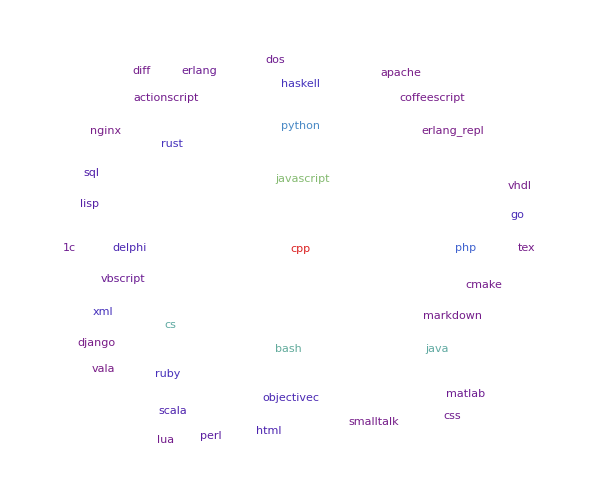
Код | Количество фрагментов кода
cpp | 5651
javascript | 2840
bash | 2232
java | 2172
cs | 2168
python | 1592
php | 1126
haskell | 605
rust | 596
xml | 587
ruby | 577
go | 517
objectivec | 482
delphi | 464
html | 431
scala | 404
sql | 352
lisp | 310
perl | 263 | -Graphics-

```mathematica
habCodeCount["Программирование",True]
```

Хаб “Веб-разработка”:

Хаб “Настройка Linux”:

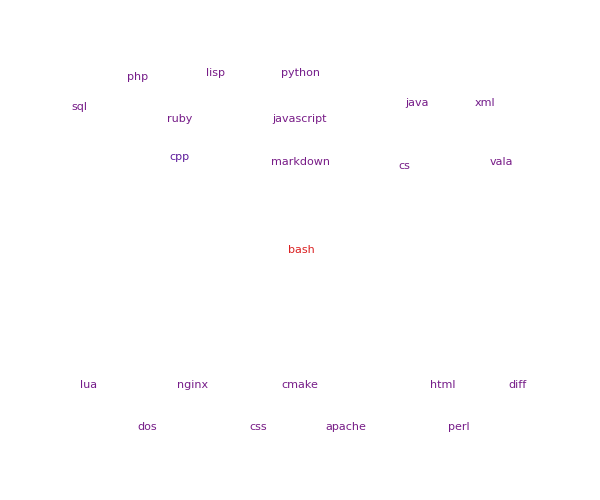
Код | Количество фрагментов кода
bash | 5650
cpp | 218
xml | 51
python | 39
lua | 34
php | 29
html | 27
nginx | 25
ruby | 23
cmake | 22
perl | 20
java | 18
dos | 18
sql | 17
diff | 17
cs | 10
apache | 9
javascript | 8
vala | 5 | -Graphics-

```mathematica
habCodeCount["Настройка Linux",True]
```

Хаб “Машинное обучение”:

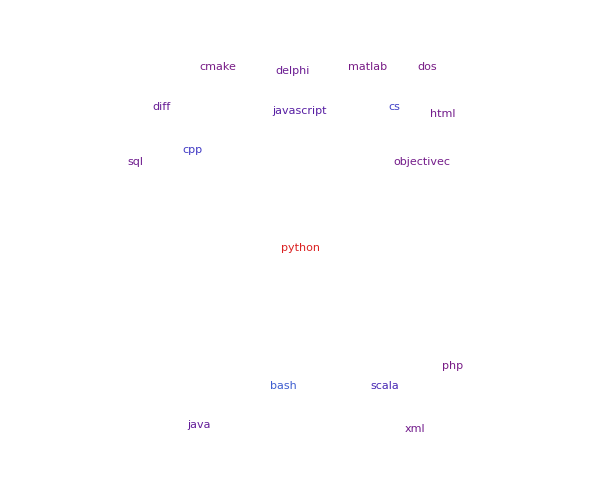
Код | Количество фрагментов кода
python | 493
bash | 95
cs | 69
cpp | 62
scala | 44
javascript | 26
java | 17
diff | 14
delphi | 11
sql | 8
xml | 6
html | 5
objectivec | 4
php | 1
matlab | 1
dos | 1
cmake | 1 | -Graphics-

```mathematica
habCodeCount["Машинное обучение",True]
```

Частота встречи слов

Сервис Яндекса “Подбор слов” очень полезен, если вы хотите написать, скажем, статью, которая будет интересна широкой аудитории. Этот сервис позволяет посмотреть частоту поисковых запросов слов. На основе подгруженной информации о статьях Хабрахабра можно сделать некий аналог этого сервиса, выдающий частоту встречи слов (их групп или регулярных выражений) в тексте статей. Это позволяет проследить интерес аудитории к той или иной теме.

Итак, создадим функцию, которая будет выдавать такого рода частоту встречаемости слов:

```mathematica
Clear[habWordFrequency]

habWordFrequency[words_String,habName_]:=habWordFrequency[{{words}},habName]

habWordFrequency[words:{_String..},habName_]:=habWordFrequency[{{words}},habName]

habWordFrequency[words_,habName_:_]:=Module[{values,gridLines,colors,wordListInner},values=Table[wordListInner=Function[WordBoundary~~#~~WordBoundary]/@wordList;Normal[habrDataset[Select[MemberQ[#Habs,habName]&],{"PublicationAbsoluteTime","PostText"}][All,{"PublicationAbsoluteTime"->(DateList[#][[{1,2}]]&),"PostText"->(StringCount[#,wordListInner]&)}][GroupBy[Key["PublicationAbsoluteTime"]],Total[Cases[#,_Integer]]&,"PostText"]],{wordList,words}];
gridLines=Table[{DatePlus[{2005,1,1},{3n,"Month"}],If[Mod[n,4]==0,Directive[{Thick,Gray}],LightGray]},{n,1,50}];
colors=ColorData[109,"ColorList"];
Legended[Show[Table[DateListPlot[values[[i]],PlotStyle->colors[[i]],PlotRange->All,GridLines->{gridLines,None},ImageSize->700,InterpolationOrder->1],{i,Length[values]}],PlotRange->All],Placed[LineLegend[colors[[1;;Length[words]]],Row[#,", "]&/@words],Bottom]]]
```

Теперь можно посмотреть разные вещи, скажем, можно сравнить, какое название ресурса “Хабрахабр” или “Хабр” чаще употребляется на Хабрахабре:

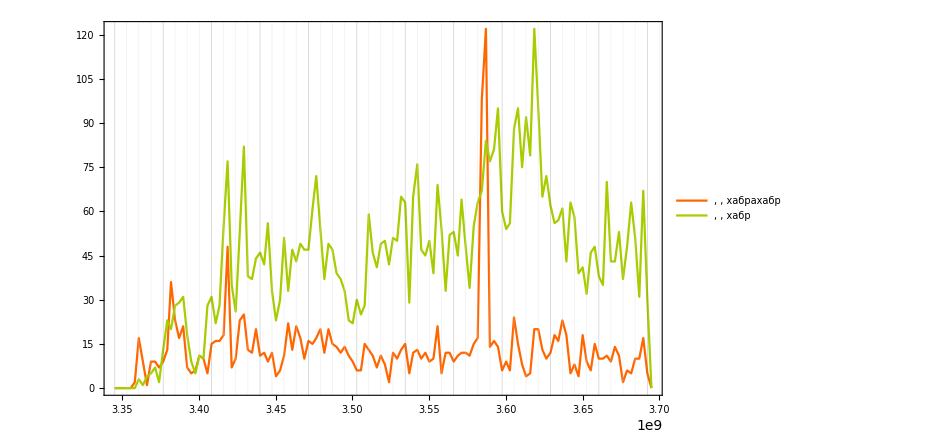

```mathematica
habWordFrequency[{{"хабрахабр"},{"хабр"}},_]
```

Или же можно сравнить частоту употребления названий различных языков программирования всюду на Хабрахабе:

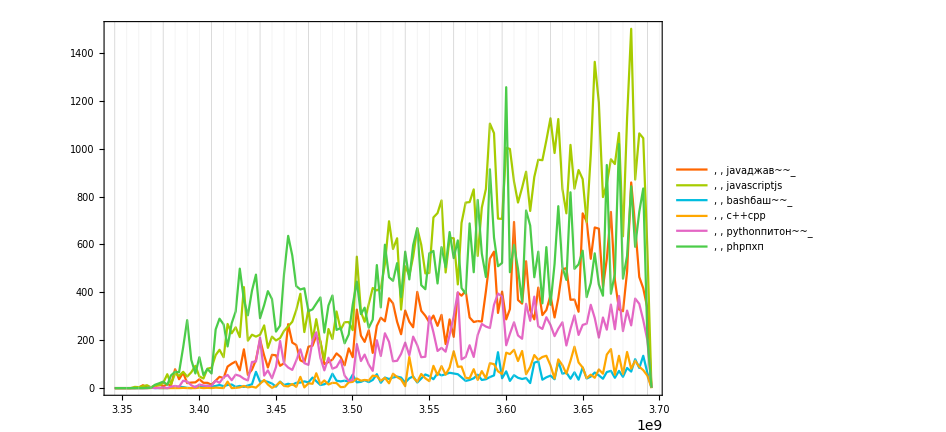

```mathematica
habWordFrequency[{{"java","джав"~~_},{"javascript","js"},{"bash","баш"~~_},{"c++","cpp"},{"python","питон"~~_},{"php","пхп"}},_]
```

Сравним частоту упоминаний математических пакетов (выражения вида “строка”~~_ (они использовались и в предыдущем примере) позволяют задавать коллекции строк с разными окончаниями, скажем, выражение “вольфрам”~~_ задаст коллекцию строк “вольфрам”, “вольфраму”, “вольфраме” и пр.):

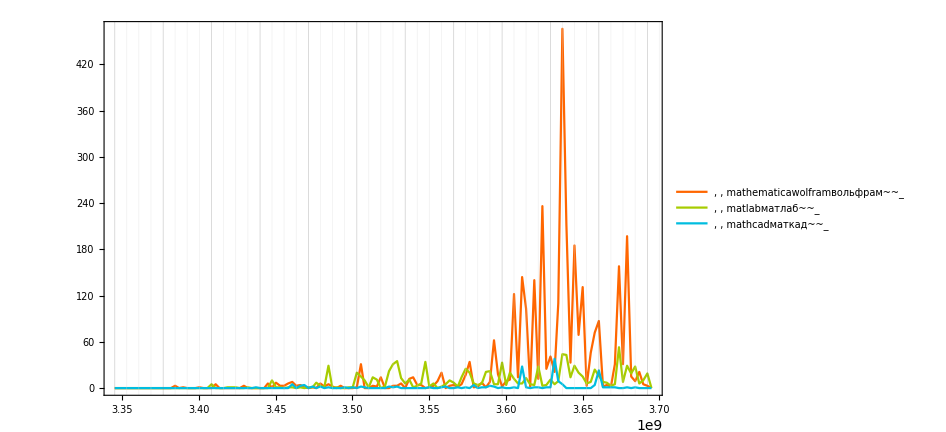

```mathematica
habWordFrequency[{{"mathematica","wolfram","вольфрам"~~_},{"matlab","матлаб"~~_},{"mathcad","маткад"~~_}},_]
```

Можно, конечно, интересоваться разными вещами, скажем, узнать частоту встреч слов группы “Россия”, “США” и “Европа”:

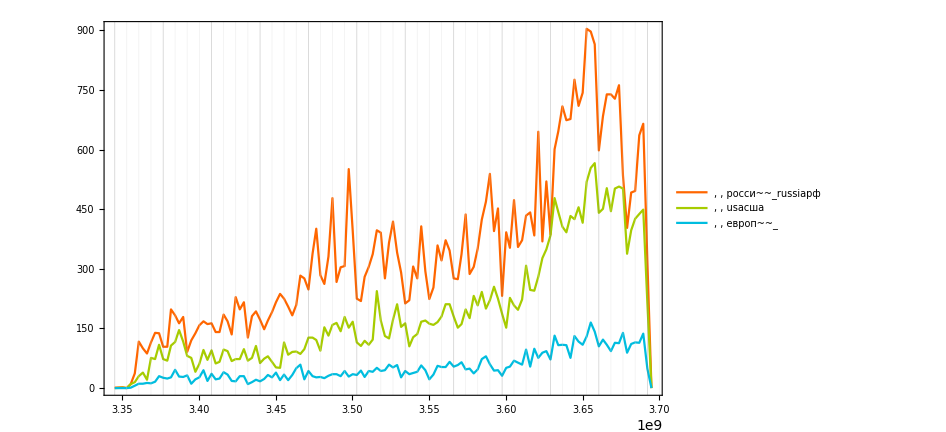

```mathematica
habWordFrequency[{{"росси"~~_,"russia","рф"},{"usa","сша"},{"европ"~~_}},_]
```

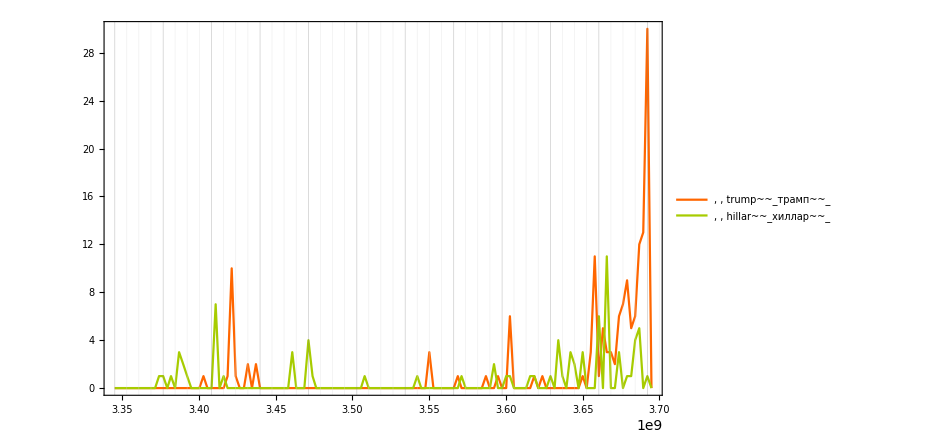

```mathematica
habWordFrequency[{{"trump"~~_,"трамп"~~_},{"hillar"~~_,"хиллар"~~_}},_]
```

Или же можно наблюдать постепенное угасание (заморозку) интереса к какой-то технологии:

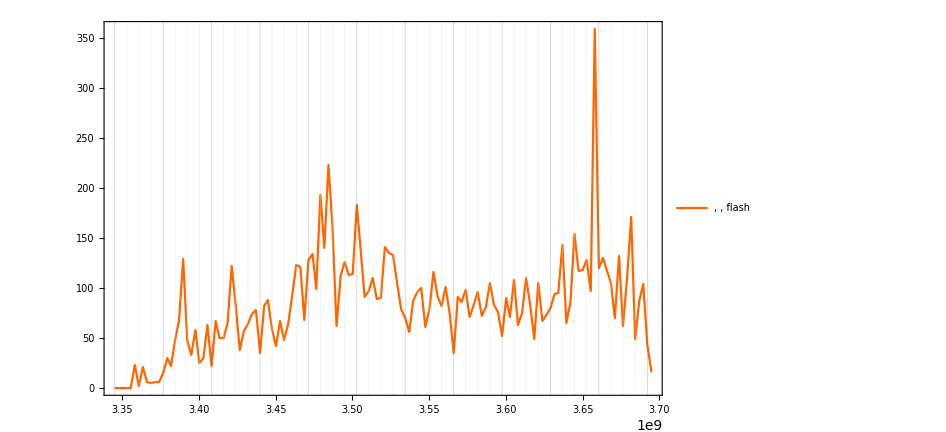

```mathematica
habWordFrequency["flash",_]
```

Или рождение новой:

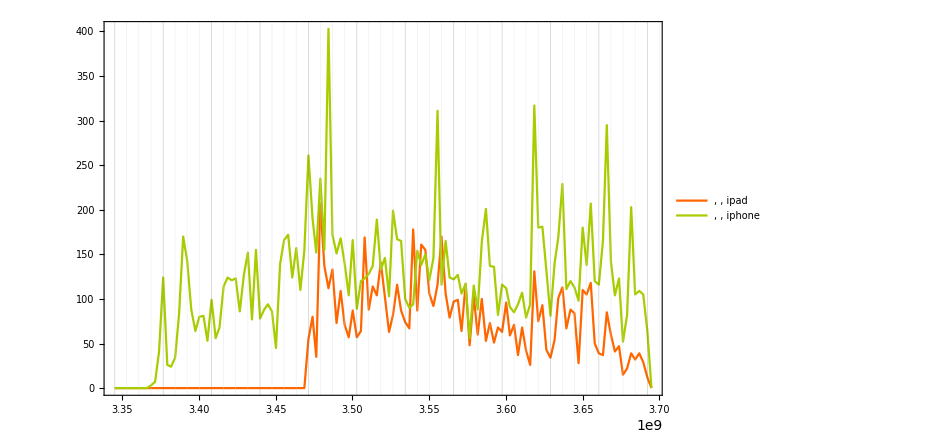

```mathematica
habWordFrequency[{{"ipad"},{"iphone"}},_]
```

Также можно смотреть на частоту употребления слов в отдельных хабах. Скажем, частота употребления слов “iOS” и “Аndroid” в хабе “Разработка под iOS”.

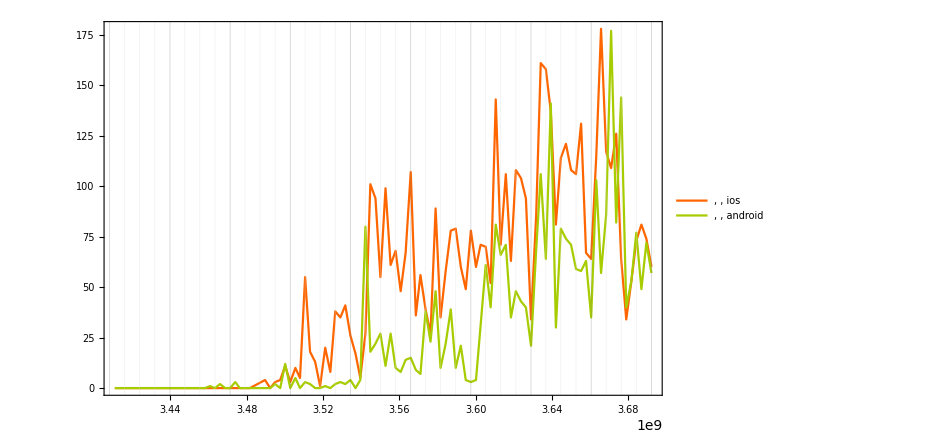

```mathematica
habWordFrequency[{{"ios"},{"android"}},"Разработка под iOS"]
```

Или те же слова, но в хабе “Разработка под Android”.

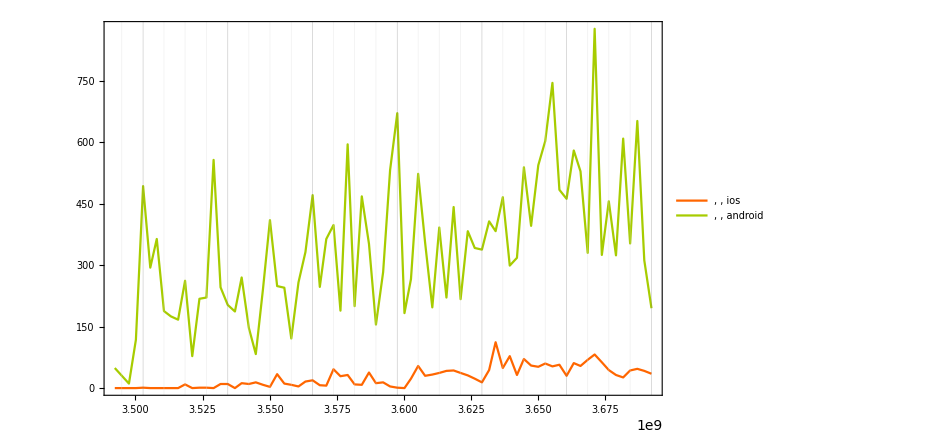

```mathematica
habWordFrequency[{{"ios"},{"android"}},"Разработка под Android"]
```

Можно сравнить частоту употребления названий операционных систем в хабе “Open source”:

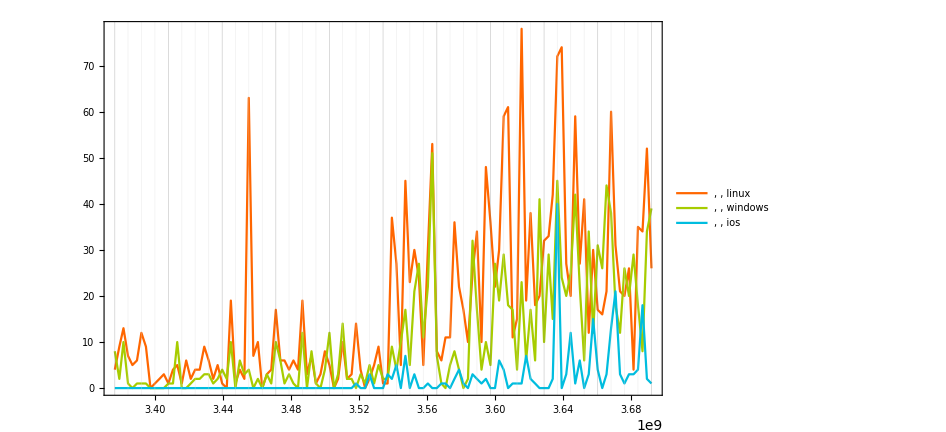

```mathematica
habWordFrequency[{{"linux"},{"windows"},{"ios"}},"Open source"]
```

с Хабрахабром в целом:

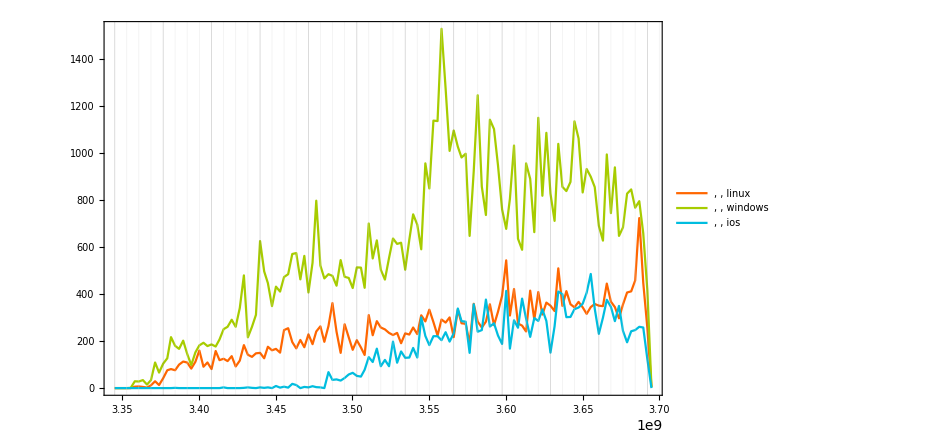

```mathematica
habWordFrequency[{{"linux"},{"windows"},{"ios"}},_]
```

Рейтинг и числа просмотров постов, а также вероятность достижения их определенных значений

Выделим пары рейтинг поста + числа просмотров поста:

```mathematica
Short[raitingAndPageViewsPairs=Normal[Values/@habrDataset[All,{"Raiting","PageViews"}]],10]
```

{{264,1700},{16,173},{28,184},{18,223},{43,970},{41,398},{26,6400},{10,318},{47,3400},{19,213},{3,291},{80,151},{39,1400},{5,2100},{43,10900},{30,4300},{20,383},{2,98},{7,192},{10,4800},{29,293},{3,7200},{150,4000},{44,2200},{13,1400},{88,1000},{24,7000},{46,2900},{98,658},{6,177},{39,466},{16,345},{8,1000},{2,174},{86,2100},«170833»,{40,9300},{29,656},{25,406},{73,71},{2,176},{9,5300},{2,736},{2,1600},{32,937},{40,972},{30,5700},{6,6600},{2,432},{17,25700},{15,7900},{22,98},{15,142},{45,79800},{14,27400},{38,12400},{50,2400},{11,7600},{4,6600},{12,110},{4,127},{27,155},{20,9700},{21,3000},{3,3600},{29,245},{9,2800},{1,3100},{3,327},{10,350},{1,1000}}

Построим их распределение на плоскости в обычном и логарифмическом масштабах:

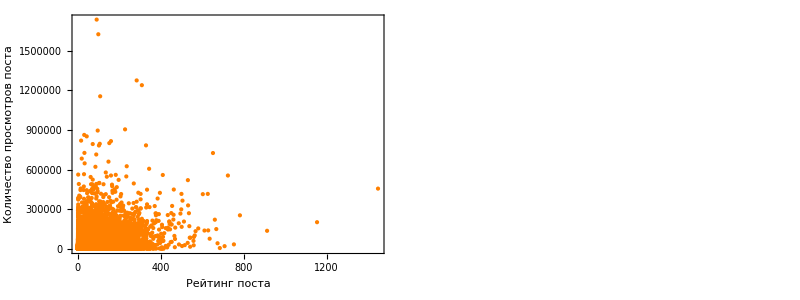

```mathematica
Grid[{{Graphics[{Orange,Point[Cases[raitingAndPageViewsPairs,{_Integer..}]]},AspectRatio->1,Frame->True,ImageSize->{500,500},FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"Рейтинг поста","Количество просмотров поста"}),ImagePadding->{{80,5},{40,5}}],Graphics[{Orange,Point[Cases[raitingAndPageViewsPairs,{x_Integer/;x>0,y_Integer}:>N@{Log10[x],Log10[y]}]]},AspectRatio->1,Frame->True,ImageSize->{500,500},FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"lg(Рейтинг поста)","lg(Количество просмотров поста)"}),ImagePadding->{{80,5},{40,5}}]}}]
```

Недостатком этих графиков является то, что они не отражают плотности распределения точек на них.

Построим двумерную и трехмерную плотность распределения рассматриваемых пар:

```mathematica
raitingAndPageViewsPairsNLog10=(Cases[raitingAndPageViewsPairs,{x_Integer/;x>0,y_Integer}:>N@{Log10[x],Log10[y]}]);
```

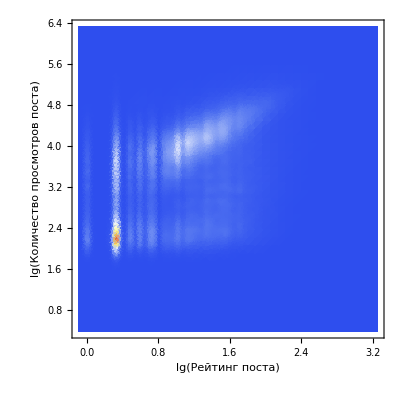
-Graphics- | -Graphics3D-

```mathematica
Grid[{{SmoothDensityHistogram[raitingAndPageViewsPairsNLog10,0.02,"PDF",AspectRatio->1,PlotRange->All,Axes->True,ImageSize->400,ColorFunction->"TemperatureMap",FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"lg(Рейтинг поста)","lg(Количество просмотров поста)"})],SmoothHistogram3D[raitingAndPageViewsPairsNLog10,0.02,"PDF",PlotRange->All,Axes->True,ImageSize->500,ColorFunction->"TemperatureMap",Mesh->None,Boxed->False,PlotPoints->80]}}]
```

Средний рейтинг поста на Хабрахабре равен 35, а среднее количество просмотров 14374.6

```mathematica
N[Mean@Cases[raitingAndPageViewsPairs,{_Integer..}]]
```

{25.6067,13487.2}

Однако, это не статистическая характеристика. Построим распределение пар (создадим распределение двумерной случайной величины):

```mathematica
empiricalDistribution=EmpiricalDistribution[N@Cases[raitingAndPageViewsPairs,{_Integer..}]]
```

DataDistribution[…]

Найдем математическое ожидание:

```mathematica
Mean@empiricalDistribution
```

{25.6067,13487.2}

А также среднеквадратическое отклонение:

```mathematica
StandardDeviation@empiricalDistribution
```

{35.9361,28783.9}

Также можно найти вероятность, например, того, что пост наберет определенный рейтинг:

```mathematica
Grid[{{"Значение рейтинга",Style["Вероятность того, что пост\nнаберет рейтинг не менее данного",TextAlignment->Center]}}~Join~Table[{n,probability=NProbability[x>=n,{x,y}\[Distributed]empiricalDistribution]},{n,Range[0,10,1]~Join~Range[20,100,10]~Join~Range[150,400,50]}],ItemStyle->{FontFamily->"Myriad Pro Cond",22},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]]
```

Значение рейтинга | Вероятность того, что пост
наберет рейтинг не менее данного
0 | 1.
1 | 1.
2 | 0.974559
3 | 0.834374
4 | 0.801806
5 | 0.764814
6 | 0.727606
7 | 0.68794
8 | 0.660474
9 | 0.632271
10 | 0.604425
20 | 0.397986
30 | 0.272347
40 | 0.192846
50 | 0.142256
60 | 0.106054
70 | 0.0804667
80 | 0.0622809
90 | 0.0493789
100 | 0.0396248
150 | 0.0146106
200 | 0.00629012
250 | 0.00292564
300 | 0.00152133
350 | 0.000766517
400 | 0.000485656

Найдем теперь вероятность, того, что пост наберет определенное число просмотров:

```mathematica
Grid[{{"Значение числа просмотров, ",Style["Вероятность того, что пост\nнаберет число просмотров не менее данного",TextAlignment->Center]}}~Join~Table[{n,probability=NProbability[y≥n,{x,y}\[Distributed]empiricalDistribution]},{n,{0,100,500,1000,2000,3000,4000,5000}~Join~Range[10000,1000000,50000]}],ItemStyle->{FontFamily->"Myriad Pro Cond",22},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]]
```

Значение числа просмотров,  | Вероятность того, что пост
наберет число просмотров не менее данного
0 | 1.
100 | 0.984769
500 | 0.751795
1000 | 0.689186
2000 | 0.623664
3000 | 0.573577
4000 | 0.530851
5000 | 0.492168
10000 | 0.346659
60000 | 0.041585
110000 | 0.0132941
160000 | 0.00579276
210000 | 0.00288468
260000 | 0.00167346
310000 | 0.00100057
360000 | 0.000637789
410000 | 0.000491507
460000 | 0.000310117
510000 | 0.000222348
560000 | 0.000169687
610000 | 0.000140431
660000 | 0.000122877
710000 | 0.000111174
760000 | 0.0000936204
810000 | 0.000064364
860000 | 0.0000468102
910000 | 0.0000292564
960000 | 0.0000292564

Зависимость рейтинга и числа просмотров поста от времени публикации

Из кода ниже видно, что за все время на Хабре все статьи набрали суммарный рейтинг порядка 2,1 млн., а суммарное количество их просмотров приближается к 1 млрд.:

```mathematica
Total@Cases[Values/@habrDataset[All,{"Raiting","PageViews"}],{_Integer..}]
```

{4376261,2304995974}

Выделим тройки время публикации поста + рейтинг поста + количество просмотров поста:

```mathematica
timeAndRaitingAndPageViewsPairs[type_]:=timeAndRaitingAndPageViewsPairs[type]=SortBy[If[type=="PublicationAbsoluteTime",Identity[#],{{#[[1,1]],N@Mean[#[[;;,2]]],N@Total[#[[;;,2]]]},{#[[1,1]],N@Mean[#[[;;,3]]],N@Total[#[[;;,3]]]}}&/@GatherBy[#,First]]&@Cases[Normal[Values/@habrDataset[All,{type,"Raiting","PageViews"}]],If[type=="PublicationDayOfWeek",{_,_Integer..},{_,_Integer..}]],First]
```

Изучим поведение рейтинга постов в зависимости от времени публикации:

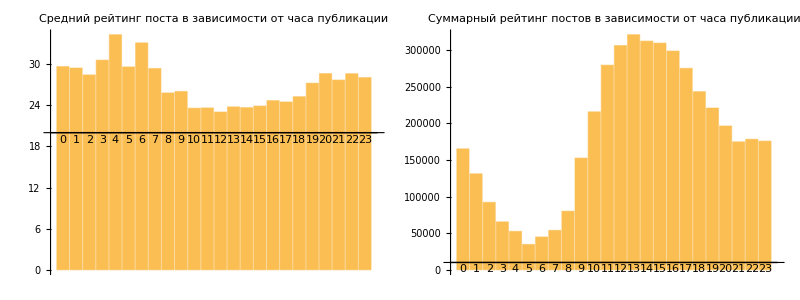

```mathematica
Grid[{{
BarChart[#[[;;,1,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{20,All}},PlotRangePadding->{Automatic,{2,1}},PlotLabel->Style["Средний рейтинг поста в зависимости от часа публикации",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,1,3]],ChartLabels->#[[;;,1,1]],ImageSize->450,PlotRange->{Automatic,{10000,All}},PlotRangePadding->{Automatic,{15000,5000}},PlotLabel->Style["Суммарный рейтинг постов в зависимости от часа публикации",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationHour"]
```

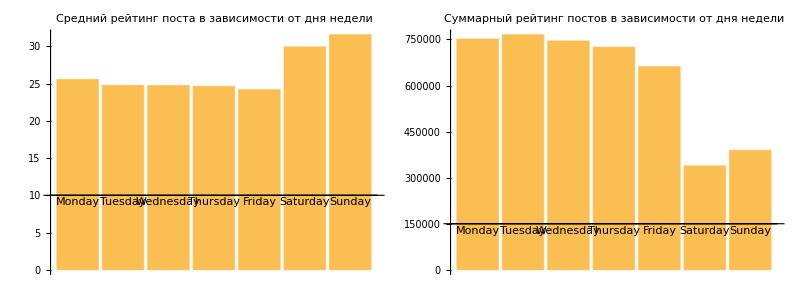

```mathematica
Grid[{{
BarChart[#[[;;,1,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{10,All}},PlotRangePadding->{Automatic,{1,1}},PlotLabel->Style["Средний рейтинг поста в зависимости от дня недели",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,1,3]],ChartLabels->#[[;;,1,1]],ImageSize->430,PlotRange->{Automatic,{150000,All}},PlotRangePadding->{Automatic,{15000,5000}},PlotLabel->Style["Суммарный рейтинг постов в зависимости от дня недели",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationDayOfWeek"][[{2,6,7,5,1,3,4}]]
```

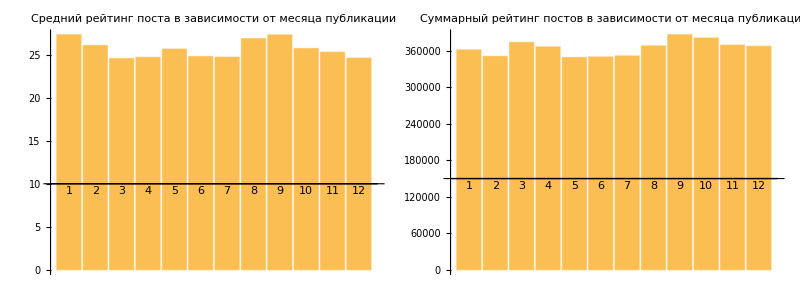

```mathematica
Grid[{{
BarChart[#[[;;,1,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{10,All}},PlotRangePadding->{Automatic,{1,1}},PlotLabel->Style["Средний рейтинг поста в зависимости от месяца публикации",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,1,3]],ChartLabels->#[[;;,1,1]],ImageSize->420,PlotRange->{Automatic,{150000,All}},PlotRangePadding->{Automatic,{5000,5000}},PlotLabel->Style["Суммарный рейтинг постов в зависимости от месяца публикации",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationMonth"]
```

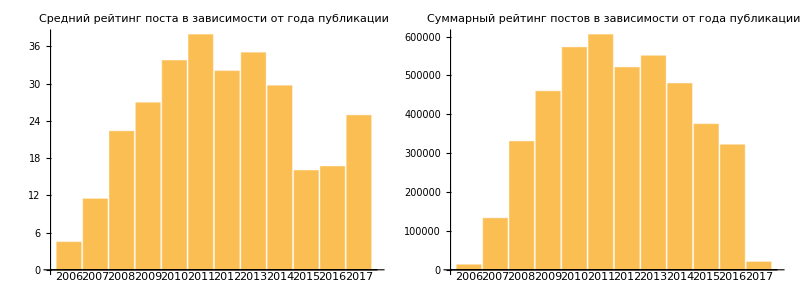

```mathematica
Grid[{{
BarChart[#[[;;,1,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{0,All}},PlotRangePadding->{Automatic,{2,1}},PlotLabel->Style["Средний рейтинг поста в зависимости от года публикации",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,1,3]],ChartLabels->#[[;;,1,1]],ImageSize->440,PlotRange->{Automatic,{0,All}},PlotRangePadding->{Automatic,{30000,5000}},PlotLabel->Style["Суммарный рейтинг постов в зависимости от года публикации",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationYear"]
```

Изучим число просмотров  постов в зависимости от времени публикации:

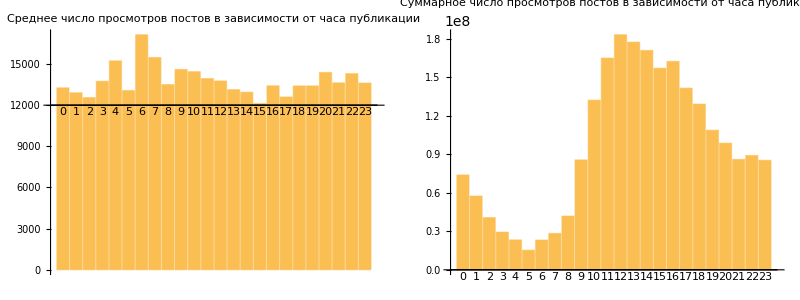

```mathematica
Grid[{{
BarChart[#[[;;,2,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{12000,All}},PlotRangePadding->{Automatic,{500,1}},PlotLabel->Style["Среднее число просмотров постов в зависимости от часа публикации",17,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,2,3]],ChartLabels->#[[;;,1,1]],ImageSize->410,PlotRange->{Automatic,{0,All}},PlotRangePadding->{Automatic,{5000000,5000}},PlotLabel->Style["Суммарное число просмотров постов в зависимости от часа публикации",17,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationHour"]
```

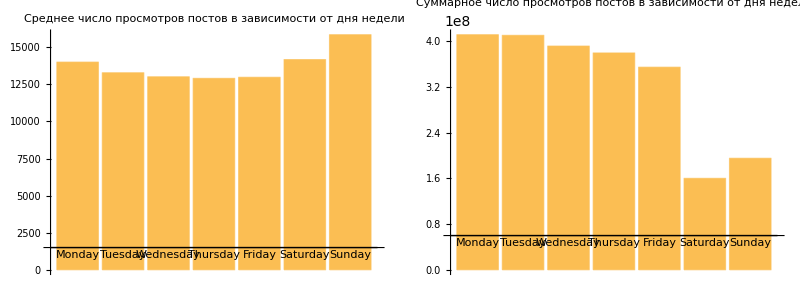

```mathematica
Grid[{{
BarChart[#[[;;,2,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{1500,All}},PlotRangePadding->{Automatic,{2000,1}},PlotLabel->Style["Среднее число просмотров постов в зависимости от дня недели",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,2,3]],ChartLabels->#[[;;,1,1]],ImageSize->420,PlotRange->{Automatic,{60000000,All}},PlotRangePadding->{Automatic,{10000000,5000000}},PlotLabel->Style["Суммарное число просмотров постов в зависимости от дня недели",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationDayOfWeek"][[{2,6,7,5,1,3,4}]]
```

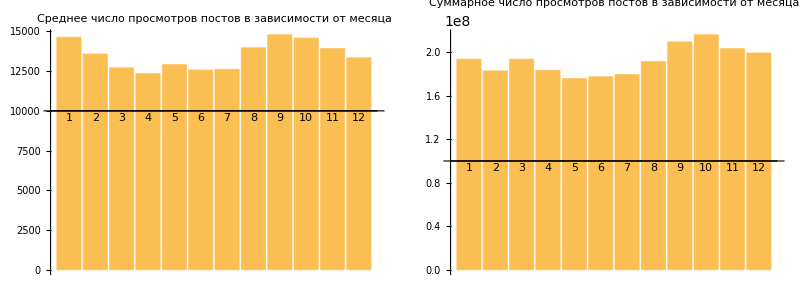

```mathematica
Grid[{{
BarChart[#[[;;,2,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{10000,All}},PlotRangePadding->{Automatic,{500,10}},PlotLabel->Style["Среднее число просмотров постов в зависимости от месяца",18,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,2,3]],ChartLabels->#[[;;,1,1]],ImageSize->415,PlotRange->{Automatic,{100000000,All}},PlotRangePadding->{Automatic,{10000000,5000000}},PlotLabel->Style["Суммарное число просмотров постов в зависимости от месяца",18,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationMonth"]
```

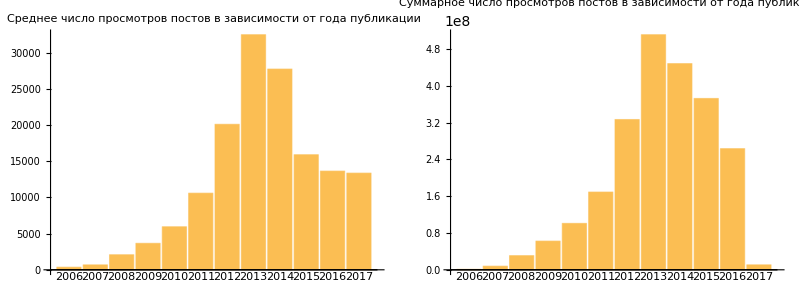

```mathematica
Grid[{{
BarChart[#[[;;,2,2]],ChartLabels->#[[;;,1,1]],ImageSize->400,PlotRange->{Automatic,{0,All}},PlotRangePadding->{Automatic,{1000,1}},PlotLabel->Style["Среднее число просмотров постов в зависимости от года публикации",17,FontFamily->"Myriad Pro Cond"]],
BarChart[#[[;;,2,3]],ChartLabels->#[[;;,1,1]],ImageSize->420,PlotRange->{Automatic,{0,All}},PlotRangePadding->{Automatic,{50000000,0}},PlotLabel->Style["Суммарное число просмотров постов в зависимости от года публикации",17,FontFamily->"Myriad Pro Cond"]]
}},Alignment->{Center,Top}]&@timeAndRaitingAndPageViewsPairs["PublicationYear"]
```

Зависимость рейтинга поста от его объема

Выделим пары вида длина поста + рейтинг поста (длина поста — мы будем ее называть далее объемом поста — врассчитывается как общее числов символов в посте):

```mathematica
Short[postLengthAndRaitingPairs=Cases[Normal[Values/@habrDataset[All,{"PostText"->StringLength,"Raiting"->Identity}][All,{"Raiting","PostText"}]],{_Integer..}],10]
```

{{264,306},{16,1095},{28,163},{18,354},{43,3120},{41,707},{26,1427},{10,3044},{47,10418},{19,2125},{3,1771},{80,1241},{39,2847},{5,343},{43,2221},{30,741},{20,1126},{2,737},{7,11847},{10,16743},{29,319},{3,3067},{150,332},{44,1836},{13,10247},{88,1078},{24,9746},{46,836},{98,1210},{6,656},{39,1225},{16,1340},{8,679},{2,4980},«170835»,{29,1614},{25,607},{73,379},{2,3876},{9,3350},{2,763},{2,10407},{32,717},{40,2082},{30,482},{6,427},{2,1053},{17,6344},{15,657},{22,629},{15,1841},{45,4781},{14,5120},{38,7241},{50,2903},{11,7895},{4,309},{12,511},{4,523},{27,643},{20,1965},{21,850},{3,1800},{29,1560},{9,2819},{1,7441},{3,2821},{10,470},{1,161}}

Построим их распределение на плоскости в обычном и логарифмическом масштабах:

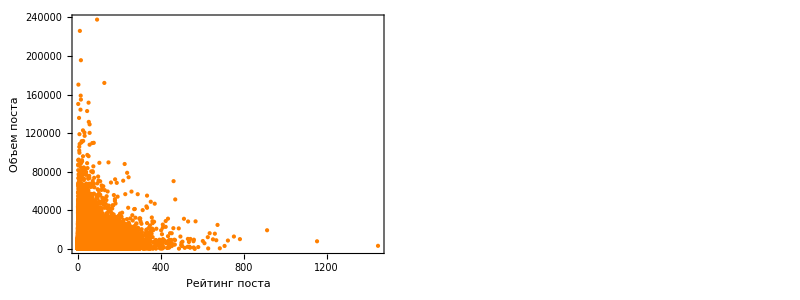

```mathematica
Grid[{{Graphics[{Orange,Point[Cases[postLengthAndRaitingPairs,{_Integer..}]]},AspectRatio->1,Frame->True,ImageSize->{500,500},FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"Рейтинг поста","Объем поста"}),ImagePadding->{{80,5},{40,5}}],Graphics[{Orange,Point[Cases[postLengthAndRaitingPairs,{x_Integer/;x>0,y_Integer/;y>0}:>N@{Log10[x],Log10[y]}]]},AspectRatio->1,Frame->True,ImageSize->{500,500},FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"lg(Рейтинг поста)","lg(Объем поста)"}),ImagePadding->{{80,5},{40,5}}]}}]
```

Построим двумерную и трехмерную плотность распределения рассматриваемых пар:

```mathematica
postLengthAndRaitingPairsNLog10=(Cases[postLengthAndRaitingPairs,{x_Integer/;x>0,y_Integer/;y>0}:>N@{Log10[x],Log10[y]}]);
```

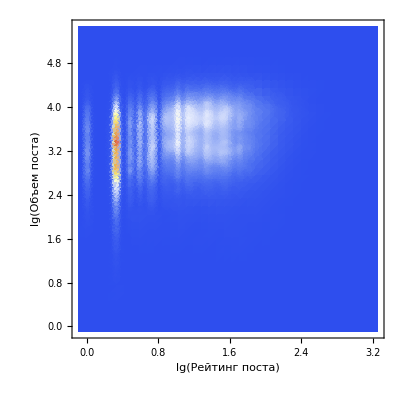
-Graphics- | -Graphics3D-

```mathematica
Grid[{{SmoothDensityHistogram[postLengthAndRaitingPairsNLog10,0.02,"PDF",AspectRatio->1,PlotRange->All,Axes->True,ImageSize->400,ColorFunction->"TemperatureMap",FrameLabel->(Style[#,FontFamily->"Myriad Pro Cond",20]&/@{"lg(Рейтинг поста)","lg(Объем поста)"})],SmoothHistogram3D[postLengthAndRaitingPairsNLog10,0.02,"PDF",PlotRange->All,Axes->True,ImageSize->500,ColorFunction->"TemperatureMap",Mesh->None,Boxed->False,PlotPoints->80]}}]
```

Средний объем поста на Хабрахабре равен 6007 символов.

```mathematica
Round@Mean[postLengthAndRaitingPairs[[;;,2]]]
```

5199

Как и раньше, построим распределение рассматриваемых пар (создадим распределение двумерной случайной величины):

```mathematica
empiricalDistribution=EmpiricalDistribution[N@Cases[postLengthAndRaitingPairs,{_Integer..}]]
```

DataDistribution[…]

Найдем вероятность того, что пост с объемом не превышающим заданное количество символов наберет рейтинг не менее заданного:

```mathematica
itemFunction=Item[#,Background->Opacity[0.8,ColorData["BrightBands"][#]]]&;

values=ParallelTable[{n,
itemFunction@NProbability[y<=n&&x>=5,{x,y}\[Distributed]empiricalDistribution],
itemFunction@NProbability[y<=n&&x>=10,{x,y}\[Distributed]empiricalDistribution],
itemFunction@NProbability[y<=n&&x>=20,{x,y}\[Distributed]empiricalDistribution],
itemFunction@NProbability[y<=n&&x>=30,{x,y}\[Distributed]empiricalDistribution],
itemFunction@NProbability[y<=n&&x>=40,{x,y}\[Distributed]empiricalDistribution]},{n,Range[0,1000,100]~Join~Range[2000,10000,1000]~Join~Range[15000,50000,5000]}];

Grid[{{Style["Объем поста менее\nзаданного числа символов",TextAlignment->Center],"P( Рейтинг > 5 )","P( Рейтинг > 10 )","P( Рейтинг > 20 )","P( Рейтинг > 30 )","P( Рейтинг > 40 )"}}~Join~values,ItemStyle->{FontFamily->"Myriad Pro Cond",22},Alignment->{Center,Center},Background->{{},{LightBlue,{LightOrange,White}}},Dividers->Directive[{Thick,LightGray}]]
```

Объем поста менее
заданного числа символов | P( Рейтинг > 5 ) | P( Рейтинг > 10 ) | P( Рейтинг > 20 ) | P( Рейтинг > 30 ) | P( Рейтинг > 40 )
0 | 5.85127×10^-6 | 5.85127×10^-6 | 5.85127×10^-6 | 5.85127×10^-6 | 5.85127×10^-6
100 | 0.00636033 | 0.00502039 | 0.00379162 | 0.00301341 | 0.00233466
200 | 0.0140372 | 0.0108132 | 0.00774123 | 0.00585712 | 0.00449963
300 | 0.0238264 | 0.0181214 | 0.0127265 | 0.00923916 | 0.00696887
400 | 0.0346629 | 0.0263424 | 0.0183262 | 0.0131244 | 0.00966045
500 | 0.0472607 | 0.035722 | 0.0245812 | 0.0174192 | 0.0126329
600 | 0.0611926 | 0.0463187 | 0.0316671 | 0.0220769 | 0.0158687
700 | 0.0759437 | 0.0572898 | 0.0390163 | 0.0269276 | 0.0191805
800 | 0.091391 | 0.0689924 | 0.0467517 | 0.0319655 | 0.0227205
900 | 0.106218 | 0.0802385 | 0.0544461 | 0.0372902 | 0.0264419
1000 | 0.121115 | 0.0916777 | 0.0621171 | 0.0423164 | 0.0298532
2000 | 0.256368 | 0.196029 | 0.131578 | 0.0887404 | 0.0615495
3000 | 0.344856 | 0.26432 | 0.17466 | 0.118283 | 0.0822279
4000 | 0.405364 | 0.31151 | 0.204853 | 0.13902 | 0.0966806
5000 | 0.459062 | 0.353165 | 0.231699 | 0.157095 | 0.109688
6000 | 0.506861 | 0.390736 | 0.255765 | 0.173186 | 0.120963
7000 | 0.548258 | 0.423439 | 0.276619 | 0.187323 | 0.130928
8000 | 0.583366 | 0.451595 | 0.294881 | 0.199885 | 0.139758
9000 | 0.613354 | 0.476153 | 0.311036 | 0.21102 | 0.147762
10000 | 0.636741 | 0.495334 | 0.323248 | 0.219721 | 0.154117
15000 | 0.708273 | 0.555496 | 0.363873 | 0.247743 | 0.17452
20000 | 0.737178 | 0.5803 | 0.38066 | 0.259756 | 0.18342
25000 | 0.749794 | 0.591294 | 0.388548 | 0.265279 | 0.187481
30000 | 0.756025 | 0.596783 | 0.392293 | 0.268041 | 0.189616
35000 | 0.759372 | 0.599644 | 0.394423 | 0.269691 | 0.190886
40000 | 0.76121 | 0.601224 | 0.395581 | 0.270487 | 0.191419
45000 | 0.762333 | 0.602236 | 0.396313 | 0.271025 | 0.191811
50000 | 0.763164 | 0.602979 | 0.396909 | 0.271464 | 0.192127